# S Shape Functions Theory: Solved Exercises

## Worked solutions to the seven exercises of section 8 of S Shape Functions Theory, with derivations, tables and plots

Dara O Shayda

Republic of Ireland

dara@compclassnotes.com

Noor Hoshino

-Graphics-

Advanced AI System Programming

Hokkaido Prefecture, Japan

noor@compclassnotes.com

Computational Classnotes · revision 1

© Computational Classnotes · CC BY-NC-SA 4.0

## Abstract

This notebook solves the seven exercises at the end of S Shape Functions Theory, called the main notebook below. Each problem is stated, solved with a derivation, checked numerically and illustrated with plots. Problem 1 repeats the staircase experiment with the arctan and algebraic sigmoids. Their tails approach the limit 1 like 1/u and 1/u^2 instead of e^-u, so every step leaks into its neighbours; to bring the leakage at N = 20 down to 10^-3 takes λ ≈ 235 for the logistic, 401 for the algebraic and 6279 for the arctan sigmoid, and a tail formula predicts these values. Problem 2 shows that σ(t) + sin(t) exp(-t^2) is sigmoidal but not monotone, overshooting to 1.068, and that its staircase still converges like 1/N, as Cybenko's theorem allows. Problem 3 uses the activations t^2 and t^3: the network can then produce only polynomials of degree 2 or 3, its hidden matrix has rank 6 or 10, and the error stops at that of the best polynomial (RMS 0.5 and 0.331), which is what the theorem of Leshno, Lin, Pinkus and Schocken predicts. Problem 4 writes x y z = exp(ln x + ln y + ln z) in the form of Kolmogorov's superposition formula and adds a four-cube identity valid for all real inputs. Problem 5 shows that one step of BasicRecurrentLayer is a Cybenko sum of the input (x, h), checks this against the real layer, and identifies the arrows that make it recurrent. Problem 6 derives the gradient with respect to the weights by the path rule, checks it against automatic differentiation and finite differences, and uses it to train an 8-unit network to a maximum error of 8 × 10^-4, 34 times smaller than an 80-unit staircase. Problem 7 predicts the staircase rates N^(-1/2) for x sin(1/x) and N to the power -ln 2/ln 3 = -0.631 for the Cantor staircase from their moduli of continuity, before measuring them, and the measurements confirm both. All results are computed in Wolfram Language, and every figure is reproducible from the numbered code cells.

Keywords: sigmoidal function; staircase approximation; tail decay; non-monotone activation; polynomial activation; Leshno–Lin–Pinkus–Schocken theorem; Kolmogorov–Arnold superposition; BasicRecurrentLayer; backpropagation; gradient descent; modulus of continuity; Cantor staircase; Wolfram Language

References of the form Eq. (M7), Figure M3, Table M3, Theorem M8 or cell c.13 of the main notebook point to S Shape Functions Theory. Equations, figures and tables of this notebook are numbered by problem: Eq. (3.2) is the second equation of Problem 3.

Every code cell starts with a comment such as (*c.3.4*) giving its index: problem 3, cell 4. Run c.0 and c.0.1 first; after that each problem runs on its own, in order. The notebook keeps its variables in a private context (CellContext -> Notebook), so definitions from other notebooks in the same session cannot interfere with it.

Main notebook: S Shape Functions Theory
https://www.wolframcloud.com/obj/ccn2/Published/S_Shape_Functions_Theory.nb

Main notebook: S Shape Functions Theory: Solved Exercises
https://www.wolframcloud.com/obj/ccn2/Published/S_Shape_Functions_Theory_Solved_Exercises.nb

CCN Node:
https://discuss.compclassnotes.com/t/s-shape-functions-theory/522

CCN Wiki:
https://wiki.compclassnotes.com/books/neural-networks/page/s-shape-functions-theory   (.md)

-Graphics-

## Index of problems, equations, figures, tables and code cells

### Problems

Problem 1. The staircase with the arctan and algebraic sigmoids (c.1.1–c.1.8)

Problem 2. A non-monotone sigmoidal function (c.2.1–c.2.6)

Problem 3. The polynomial activation t^2 (c.3.1–c.3.6)

Problem 4. x y z as a Kolmogorov superposition (c.4.1–c.4.6)

Problem 5. One step of BasicRecurrentLayer as a Cybenko sum (c.5.1–c.5.6)

Problem 6. The gradient with respect to the weights (c.6.1–c.6.7)

Problem 7. Predicting rates from the modulus of continuity (c.7.1–c.7.7)

### Equations

(1.1)–(1.5)  tails, steepness for a given tail, ideal staircase, leakage, required λ

(2.1)–(2.2)  the non-monotone S-shape, an error bound

(3.1)–(3.3)  a network with t^2 is a quadratic, dimension count, best polynomials

(4.1)–(4.3)  the product as exp of a sum, its Kolmogorov form, the four-cube identity

(5.1)–(5.3)  the recurrent step, the step as a Cybenko sum, unrolling

(6.1)–(6.4)  the three weight gradients, the loss and its gradient

(7.1)–(7.4)  the staircase bound, the moduli of x sin(1/x) and of the Cantor staircase

### Figures

Figure 1.1–1.4. S-shapes and tails, staircases, leakage against λ, leakage at the nodes

Figure 2.1–2.4. the non-monotone S-shape, its steepening, its staircase, convergence

Figure 3.1–3.3. error floors, singular values, the learned surfaces

Figure 4.1–4.3. the Kolmogorov network for x y z, the path of one input, level sets

Figure 5.1–5.4. one step as in Figure M3, recurrent arrows, unrolling, the two computations

Figure 6.1–6.3. training loss, the fit while training, the trained units

Figure 7.1–7.4. the targets, moduli of continuity, rates, the error along x

### Tables

Table 1.1–1.4. tails, Table M3 repeated, leakage measured and predicted, required λ

Table 2.1–2.2. properties of the non-monotone S-shape, errors for three amplitudes

Table 3.1–3.3. errors for three activations, best polynomials, ranks

Table 5.1. weights of the layer and the agreement of the three computations

Table 6.1–6.3. gradients checked, training history, trained network against staircases

Table 7.1–7.3. moduli of continuity, predicted and measured errors, rates

## Settings and shared definitions

Settings for all figures and tables, as in the main notebook. figFont and tabFont set the font sizes of every figure and every table; wFull and wHalf keep every figure inside an A4 page when the notebook is printed or saved as PDF. logLine and logText draw reference lines and labels on log-log plots.

```mathematica
(*c.0*)
figFont = 14;   (* font size in figures and diagrams *)
tabFont = 10;   (* font size in tables *)
wFull = 440;    (* full figure width in points; A4 text width is ~487 *)
wHalf = 215;    (* width of each panel in a two-column figure *)
figStyle = Directive[Black, FontSize -> figFont];
table[rows_, label_] := Labeled[
   Grid[rows, Frame -> All, Alignment -> Left,
    BaseStyle -> {FontSize -> tabFont}, Spacings -> {0.8, 0.5},
    Background -> {None, {1 -> GrayLevel[0.92]}}],
   Style[label, Bold, FontSize -> tabFont + 1], Top];
panel[opts___] :=
  Sequence[opts, LabelStyle -> figStyle, ImageSize -> wHalf];
figure[rows_, label_] := Labeled[Grid[rows], Style[label, figFont], Top];
sci[x_] := ScientificForm[x, 2];
(* reference lines and labels on log-log plots, given in plot units *)
logLine[pts_] := {Gray, Dashed, Line[Log[N[pts]]]};
logText[str_, pt_] := Text[Style[str, figFont - 2, Gray], Log[N[pt]]];
```

Example A of the main notebook, f(x) = sin(2πx) + x.b2/2, and a vectorized version of the staircase of Eq. (M7) that accepts any S-shape. The last line checks it against stair of cell c.8 of the main notebook; the difference is at the level of rounding.

```mathematica
(*c.0.1*)
(* example A of the main notebook, section 4 *)
f[x_] := Sin[2 Pi x] + x^2/2;
(* the staircase of Eq. (M7) for any S-shape s, on a list of points xs;
   vals = values of the target at the nodes 0, 1/N, ..., 1 *)
stairOn[s_, vals_, lam_, xs_] := Module[{n = Length[vals] - 1, c},
   c = N[(Range[n] - 1/2)/n];
   vals[[1]] + s[lam Outer[Subtract, N[xs], c]] . Differences[N[vals]]];
nodes[n_] := N[Range[0, n]/n];
xsFine = Range[0., 1., 0.0005];
supErrS[s_, fun_, n_, lam_] :=
  Max@Abs[fun[xsFine] - stairOn[s, fun[nodes[n]], lam, xsFine]];
(* check: stairOn agrees with stair of the main notebook, c.8 *)
stair[fun_, n_, lam_][x_] := fun[0] +
   Sum[(fun[k/n] - fun[(k - 1)/n]) *
     LogisticSigmoid[lam (x - (k - 1/2)/n)], {k, 1, n}];
Max@Abs[stairOn[LogisticSigmoid, f[nodes[10]], 200, {0.13, 0.5, 0.77}] -
   (stair[f, 10, 200] /@ {0.13, 0.5, 0.77})]
```

2.22045×10^-16

## 1. Problem 1: the staircase with arctan and algebraic sigmoids

Problem 1. Repeat the staircase experiment of section 4 (Table M3) with the arctan and algebraic sigmoids. Why do you need a larger λ for the same error?

### The three S-shapes and their tails

The three functions are the logistic σ(t) = 1/(1 + e^-t), the arctan sigmoid 1/2 + arctan(t)/π and the algebraic sigmoid (1 + t/√(1 + t^2))/2. All three are sigmoidal in the sense of Eq. (M1) and all three are symmetric, σ(-t) = 1 - σ(t). What separates them is how fast they reach their limits. Write T(u) = 1 - σ(u) for the tail, the distance from the limit 1 at u > 0. By symmetry the same T(u) is the distance from the limit 0 at -u. As u → ∞,

1-σ(u)∼Piecewise[{{e^-u, logistic}, {1/πu, arctan}, {1/(4 u^2), algebraic}}]   u→∞        (1.1)

The logistic tail is exponential; the other two are algebraic, and the arctan tail is the slowest of all: at u = 1000 it is still 3 × 10^-4. Solving T(u) = η for u gives the steepness at which each function is within η of its limit:

u_η=Piecewise[{{log((1-η)/η), logistic}, {cot(πη), arctan}, {(1-2η)/(2 √(η(1-η))), algebraic}}]        (1.2)

For η = 10^-6 the logistic needs u ≈ 14, the algebraic sigmoid u ≈ 500 and the arctan sigmoid u ≈ 318000: the logistic grows like ln(1/η), the algebraic like 1/(2√η) and the arctan like 1/(πη).

Figure 1.1. Left: the three S-shapes. Right: their tails 1 - σ(u) on log-log axes, with the leading terms 1/(πu) and 1/(4u^2) of Eq. (1.1) dashed. The logistic tail falls off the bottom of the plot near u = 18.

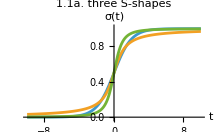
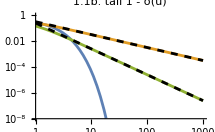
-Graphics- | -Graphics-Figure 1.1. The three S-shapes and their tails

```mathematica
(*c.1.1*)
sig3 = <|"logistic" -> LogisticSigmoid,
   "arctan" -> (1/2 + ArcTan[#]/Pi &),
   "algebraic" -> ((1 + #/Sqrt[1 + #^2])/2 &)|>;
(* the tail 1 - σ(u): distance to the limit 1. All three satisfy
   σ(-u) = 1 - σ(u), so σ(-u) gives the tail without round-off *)
tail[k_][u_] := sig3[k][-u];
figure[{{
   Plot[Evaluate[Through[Values[sig3][t]]], {t, -10, 10},
    PlotRange -> {-0.02, 1.02}, AxesLabel -> {"t", "σ(t)"},
    PlotLegends -> Placed[LineLegend[Keys[sig3],
       LabelStyle -> Directive[figFont - 3]], Below],
    Evaluate@panel[PlotLabel -> "1.1a. three S-shapes"]],
   Quiet@LogLogPlot[Evaluate@Join[Table[tail[k][u], {k, Keys[sig3]}],
      {1/(Pi u), 1/(4 u^2)}], {u, 1, 1000},
    PlotRange -> {10^-8, 1}, Ticks -> {{1, 10, 100, 1000}, Automatic},
    PlotStyle -> Join[ColorData[97] /@ {1, 2, 3},
      Table[Directive[Black, Dashed], 2]],
    Evaluate@panel[PlotLabel -> "1.1b. tail 1 - σ(u)"]]}},
 "Figure 1.1. The three S-shapes and their tails"]
```

Table 1.1. Each tail divided by its leading term tends to 1, as Eq. (1.1) states. The closed forms u(η) of Eq. (1.2), a numerical check of them, and their values.

```mathematica
(*c.1.2*)
(* leading term of each tail, Eq. (1.1) *)
lead = <|"logistic" -> Exp[-u], "arctan" -> 1/(Pi u),
   "algebraic" -> 1/(4 u^2)|>;
(* the steepness u at which the tail falls to η, Eq. (1.2) *)
uOf = <|"logistic" -> Log[(1 - η)/η], "arctan" -> Cot[Pi η],
   "algebraic" -> (1 - 2 η)/(2 Sqrt[η (1 - η)])|>;
table[Prepend[
  Table[{k, Limit[tail[k][u]/lead[k], u -> Infinity],
    TraditionalForm[uOf[k]],
    sci@Max@Table[Abs[tail[k][uOf[k]] - η]/η,
      {η, 10.^-Range[1, 6]}],
    Sequence @@ Table[NumberForm[N[uOf[k] /. η -> e], 4],
      {e, {10^-2, 10^-3, 10^-6}}]}, {k, Keys[sig3]}],
  {"σ", "tail / lead", "u(η)", "check: rel. error",
   "η = 0.01", "η = 0.001", Row[{"η = ", Superscript[10, -6]}]}],
 "Table 1.1"]
```

σ | tail / lead | u(η) | check: rel. error | η = 0.01 | η = 0.001 | η = 10^-6
logistic | 1 | log((1-η)/η) | 8.5×10^-16 | 4.595 | 6.907 | 13.82
arctan | 1 | cot(π η) | 2.7×10^-11 | 31.82 | 318.3 | 318300.
algebraic | 1 | (1-2 η)/(2 √((1-η) η)) | 2.7×10^-11 | 4.925 | 15.79 | 500.Table 1.1

### Table M3 repeated

First the experiment as asked: the staircase G_N of Eq. (M7), with steepness λ = 20 N as in Table M3, built from each of the three S-shapes, and its largest error on [0, 1] for example A.

Table 1.2. Sup-norm error of G_N for example A with each S-shape, λ = 20 N.

```mathematica
(*c.1.3*)
(* Table M3, row A, repeated with each S-shape, λ = 20 N *)
table[Prepend[
  Table[Prepend[Table[NumberForm[supErrS[sig3[k], f, n, 20 n], 3],
     {n, {5, 10, 20, 40, 80}}], k], {k, Keys[sig3]}],
  {"σ", "N = 5", "N = 10", "N = 20", "N = 40", "N = 80"}], "Table 1.2"]
```

σ | N = 5 | N = 10 | N = 20 | N = 40 | N = 80
logistic | 0.442 | 0.22 | 0.11 | 0.0551 | 0.0276
arctan | 0.401 | 0.186 | 0.0961 | 0.0518 | 0.027
algebraic | 0.5 | 0.252 | 0.126 | 0.063 | 0.0316Table 1.2

A surprise: at λ = 20 N the three errors are almost the same, and the arctan staircase is even slightly better. The sup-norm error here is dominated by the coarseness of the staircase, which is O(1/N) whatever the S-shape, and a softer step even rounds the corners of the staircase a little. To see where the S-shape matters, compare G_N with the ideal staircase S_N of hard steps, the limit λ → ∞ used in the proof of Lemma M1:

S_N(x)=f(0)+∑_(k=1)^N Δ_k H(x-c_k)
Δ_k=f(k/N)-f((k-1)/N),  c_k=(k-1/2)/N,  S_N(k/N)=f(k/N)        (1.3)

S_N is exact at the nodes k/N, which lie halfway between two step positions c_k. So any error of G_N at a node is caused by the tails of the steps alone. We call it leakage.

Figure 1.2. Top: G_10 with λ = 200 for the three S-shapes, nearly indistinguishable. Bottom: the distance |G_10 - S_10| on a log scale. At the nodes (grid lines) it falls to about 10^-6 for the logistic and to between 10^-4 and 10^-3 for the algebraic sigmoid, and stays near 10^-2 for the arctan sigmoid.

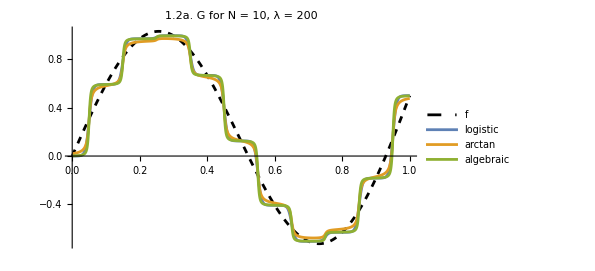
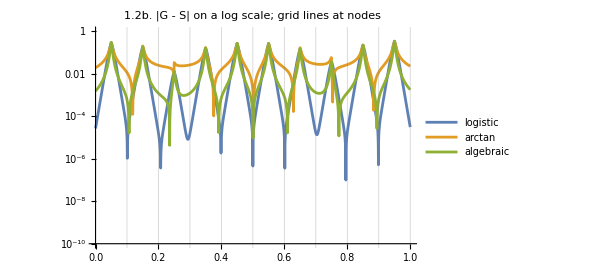
-Graphics-
-Graphics-Figure 1.2. Staircases with the three S-shapes

```mathematica
(*c.1.4*)
(* the ideal staircase S_N of hard steps, Eq. (1.3) *)
stepStair[vals_, xs_] := stairOn[UnitStep, vals, 1, xs];
gAll = Table[stairOn[sig3[k], f[nodes[10]], 200, xsFine],
   {k, Keys[sig3]}];
figure[{{
   ListLinePlot[Prepend[Transpose[{xsFine, #}] & /@ gAll,
     Transpose[{xsFine, f[xsFine]}]],
    PlotStyle -> Prepend[ColorData[97] /@ {1, 2, 3},
      Directive[Black, Dashed]], PlotRange -> All,
    PlotLegends -> Placed[LineLegend[Prepend[Keys[sig3], "f"],
       LabelStyle -> Directive[figFont - 3]], Below],
    PlotLabel -> "1.2a. G for N = 10, λ = 200",
    LabelStyle -> figStyle, ImageSize -> wFull]}, {
   ListLogPlot[Transpose[{xsFine, Abs[# - stepStair[f[nodes[10]],
          xsFine]] + 10.^-16}] & /@ gAll,
    Joined -> True, PlotStyle -> ColorData[97] /@ {1, 2, 3},
    PlotRange -> {10^-10, 1}, GridLines -> {nodes[10], None},
    PlotLegends -> Placed[LineLegend[Keys[sig3],
       LabelStyle -> Directive[figFont - 3]], Below],
    PlotLabel -> "1.2b. |G - S| on a log scale; grid lines at nodes",
    LabelStyle -> figStyle, ImageSize -> wFull]}},
 "Figure 1.2. Staircases with the three S-shapes"]
```

### The leakage and its formula

At a node x_k every step to its left has risen to 1 - T and every step to its right has risen to T. With the symmetry σ(-u) = 1 - σ(u), the leakage is exactly

G_N(x_k)-f(x_k)=-∑_m sgn(x_k-c_m) Δ_m T(λ|x_k-c_m|)
T(u)=1-σ(u)=σ(-u),  x_k=k/N        (1.4)

Each jump Δ_m of f contributes its height times the tail at the scaled distance from the node. Replacing T by its leading term from Eq. (1.1) turns Eq. (1.4) into a prediction, without any fitting. For the logistic only the two nearest steps, at distance 1/(2N), matter, and the leakage falls like exp(-λ/(2N)). For the algebraic sigmoid every step contributes and the leakage falls like 1/λ^2. For the arctan sigmoid it falls only like 1/λ, and the sum over all steps does not cancel.

Table 1.3. Leakage at N = 20, measured and predicted by Eq. (1.4). From λ = 400 on, the predictions agree with the measurements to two digits. The logistic measurement stops at 6 × 10^-17, the rounding level of machine numbers.

```mathematica
(*c.1.5*)
(* leakage: error at the nodes k/N, where the ideal staircase is exact *)
leakAt[s_, n_, lam_] :=
  stairOn[s, f[nodes[n]], lam, nodes[n]] - f[nodes[n]];
leak[s_, n_, lam_] := Max@Abs@leakAt[s, n, lam];
(* prediction of Eq. (1.4): each tail replaced by its leading term *)
predAt[k_, n_, lam_] := Quiet@Module[
   {d = Differences[f[nodes[n]]], c = N[(Range[n] - 1/2)/n]},
   Table[-Total[Sign[x - c] d (lead[k] /. u -> lam Abs[x - c])],
    {x, nodes[n]}]];
predLeak[k_, n_, lam_] := Max@Abs@predAt[k, n, lam];
lams = {100, 400, 1600, 6400, 25600};
table[Prepend[
  Flatten[Table[{
     {k, "measured", Sequence @@ (sci@leak[sig3[k], 20, #] & /@ lams)},
     {"", "Eq. (1.4)", Sequence @@ (sci@predLeak[k, 20, #] & /@ lams)}},
    {k, Keys[sig3]}], 1],
  Join[{"σ", ""}, ("λ = " <> ToString[#] &) /@ lams]], "Table 1.3"]
```

σ |  | λ = 100 | λ = 400 | λ = 1600 | λ = 6400 | λ = 25600
logistic | measured | 2.7×10^-2 | 1.6×10^-5 | 1.1×10^-16 | 1.1×10^-16 | 1.1×10^-16
 | Eq. (1.4) | 3.×10^-2 | 1.6×10^-5 | 1.5×10^-18 | 1.2×10^-70 | 4.×10^-279
arctan | measured | 6.×10^-2 | 1.6×10^-2 | 3.9×10^-3 | 9.8×10^-4 | 2.5×10^-4
 | Eq. (1.4) | 6.3×10^-2 | 1.6×10^-2 | 3.9×10^-3 | 9.8×10^-4 | 2.5×10^-4
algebraic | measured | 1.5×10^-2 | 1.×10^-3 | 6.3×10^-5 | 4.×10^-6 | 2.5×10^-7
 | Eq. (1.4) | 1.6×10^-2 | 1.×10^-3 | 6.3×10^-5 | 4.×10^-6 | 2.5×10^-7Table 1.3

Figure 1.3. Leakage against λ at N = 20. The logistic plunges, the algebraic sigmoid follows slope -2 and the arctan sigmoid slope -1, as Eq. (1.4) predicts.

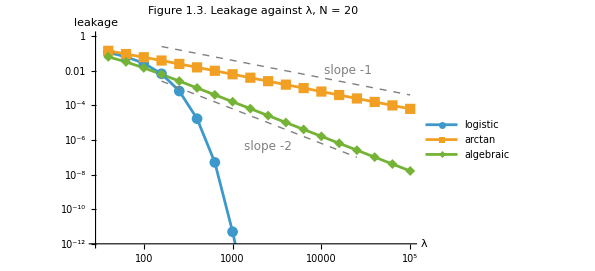

```mathematica
(*c.1.6*)
ListLogLogPlot[
 Table[Table[{lam, Max[leak[sig3[k], 20, lam], 10.^-16]},
   {lam, 10^Range[1.6, 5, 0.2]}], {k, Keys[sig3]}],
 Joined -> True, PlotMarkers -> Automatic, PlotRange -> {10^-12, 1},
 AxesLabel -> {"λ", "leakage"},
 Epilog -> {logLine[{{10^2.2, 10^-0.6}, {10^5, 10^-3.4}}],
   logLine[{{10^2.2, 10^-2.6}, {10^4.4, 10^-7.}}],
   logText["slope -1", {10^4.3, 10^-2.}],
   logText["slope -2", {10^3.4, 10^-6.4}]},
 PlotLegends -> Placed[LineLegend[Keys[sig3], LabelStyle -> figStyle],
   Below],
 PlotLabel -> "Figure 1.3. Leakage against λ, N = 20",
 LabelStyle -> figStyle, ImageSize -> wFull]
```

### How large must λ be?

Setting the leakage equal to a tolerance η and solving for λ gives the answer to the question. Write L_1 and L_2 for the largest leakage of the arctan and algebraic sigmoids at λ = 1, computed from Eq. (1.4) with the leading terms; then the leakage is L_1/λ and L_2/λ^2, and

λ_logistic≈2N log((|Δ_N|)/η),    λ_arctan≈L_1/η,    λ_algebraic≈√(L_2/η)        (1.5)

Table 1.4. The λ needed for a leakage of 10^-3, found by root finding, against Eq. (1.5).

```mathematica
(*c.1.7*)
(* the λ that brings the leakage down to η = 10^-3, measured *)
lamNeed[s_, n_, eta_] := Exp[l /. FindRoot[
     Log[Max[leak[s, n, Exp[l]], 10.^-300]] == Log[eta],
     {l, Log[40. n]}]];
(* and predicted: logistic from the end point, the others from
   Eq. (1.4) scaled by 1/λ or 1/λ.b2, Eq. (1.5) *)
lamPred[n_, eta_] := {
   2 n Log[Abs[Last@Differences[f[nodes[n]]]]/eta],
   predLeak["arctan", n, 1]/eta,
   Sqrt[predLeak["algebraic", n, 1]/eta]};
table[Prepend[
  Flatten[Table[{
     {n, "measured", Sequence @@ (Round[lamNeed[sig3[#], n, 10.^-3]] &
         /@ Keys[sig3])},
     {"", "Eq. (1.5)", Sequence @@ Round[lamPred[n, 10.^-3]]}},
    {n, {10, 20, 40}}], 1],
  {"N", "", "logistic", "arctan", "algebraic"}], "Table 1.4"]
```

N |  | logistic | arctan | algebraic
10 | measured | 130 | 5790 | 268
 | Eq. (1.5) | 131 | 5790 | 268
20 | measured | 235 | 6279 | 401
 | Eq. (1.5) | 235 | 6279 | 403
40 | measured | 415 | 7903 | 581
 | Eq. (1.5) | 416 | 7903 | 585Table 1.4

For N = 20 the arctan sigmoid needs λ ≈ 6300, 27 times more than the logistic; the algebraic sigmoid needs 1.7 times more. The logistic requirement grows roughly in proportion to N and the arctan requirement only logarithmically (through L_1), so the ratio shrinks as N grows, but for any tolerance the order logistic < algebraic < arctan holds, and the gap widens as η shrinks, because of Eq. (1.2).

Figure 1.4. The signed leakage at every node, N = 20, λ = 400. For the logistic and algebraic sigmoids the contributions of neighbouring steps cancel in the interior. For the arctan sigmoid they do not: the leakage follows the shape of -sin(2πx), and Eq. (1.4) (dashed) reproduces it point by point.

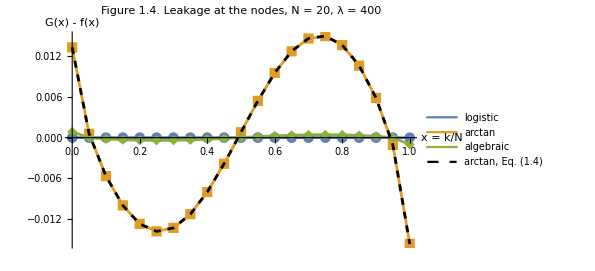

```mathematica
(*c.1.8*)
(* where the leakage sits: signed error at each node, N = 20, λ = 400;
   dashed: the arctan prediction of Eq. (1.4) *)
Legended[Show[
  ListPlot[Table[Transpose[{nodes[20], leakAt[sig3[k], 20, 400]}],
    {k, Keys[sig3]}], Joined -> True, PlotMarkers -> Automatic,
   PlotStyle -> (ColorData[97] /@ {1, 2, 3}), PlotRange -> All,
   AxesLabel -> {"x = k/N", "G(x) - f(x)"},
   PlotLabel -> "Figure 1.4. Leakage at the nodes, N = 20, λ = 400",
   LabelStyle -> figStyle, ImageSize -> wFull],
  ListLinePlot[Transpose[{nodes[20], predAt["arctan", 20, 400]}],
   PlotStyle -> Directive[Black, Dashed]]],
 Placed[LineLegend[Append[ColorData[97] /@ {1, 2, 3},
    Directive[Black, Dashed]], Append[Keys[sig3], "arctan, Eq. (1.4)"],
   LabelStyle -> Directive[figFont - 3], LegendLayout -> "Row"], Below]]
```

The shape in Figure 1.4 has a name. With T(u) ≈ 1/(πu), Eq. (1.4) becomes, for large N, -(1/(πλ)) times the principal-value integral of f′(s)/(x - s) over [0, 1]: a truncated Hilbert transform of f′. The Hilbert transform of a cosine is a sine, and f′ is dominated by 2π cos(2πx). A tail as heavy as 1/u reaches every step of the staircase.

### Answer

With λ = 20 N, as in Table M3, the three S-shapes give almost the same sup-norm error, because the error is set by the coarseness of the staircase. The S-shape matters in how quickly G_N approaches the ideal staircase of hard steps, which is the limit used in Cybenko's proof. A sigmoid reaches its limits at the rate of its tail, Eq. (1.1): exponentially for the logistic, like 1/u^2 for the algebraic and like 1/u for the arctan sigmoid. Each step leaks its tail into the neighbouring nodes, Eq. (1.4), so the slower the tail, the larger λ must be for the same leakage, Eq. (1.5) and Table 1.4. For a leakage of 10^-3 at N = 20: λ ≈ 235, 401 and 6279.

## 2. Problem 2: a sigmoidal function that is not monotone

Problem 2. Try a non-monotone function such as σ(t) + sin(t) exp(-t^2). Is it sigmoidal in the sense of Eq. (M1), and does the staircase still converge?

### Is it sigmoidal?

Write s for the new function:

s(t)=σ(t)+sin t e^(-t^2),    lim_(t→-∞) s(t)=0,  lim_(t→+∞) s(t)=1        (2.1)

Since |sin(t) exp(-t^2)| ≤ exp(-t^2) → 0, the added term disappears at both ends and the limits are those of σ: 0 and 1. That is all Eq. (M1) asks for, so s is sigmoidal. It is also continuous, and it keeps the symmetry s(-t) = 1 - s(t), because sin is odd. But it is not monotone. Its derivative changes sign four times in (-4, 4). s rises above 1, to 1.068 at t = 0.784, and by symmetry dips below 0, to -0.068 at t = -0.784.

Table 2.1. Properties of s, computed symbolically and numerically.

```mathematica
(*c.2.1*)
s2[t_] := LogisticSigmoid[t] + Sin[t] Exp[-t^2];
{tMax, tMin} = t /. {Last[#], First[#]} &@
    NSolve[D[s2[t], t] == 0 && -1 < t < 1, t];
table[{
  {"property", "value"},
  {"limit t → -∞", Limit[s2[t], t -> -Infinity]},
  {"limit t → +∞", Limit[s2[t], t -> Infinity]},
  {"sigmoidal, Eq. (M1)?", "yes"},
  {"σ(-t) = 1 - σ(t)?", FullSimplify[s2[-t] == 1 - s2[t]]},
  {"largest value", Row[{NumberForm[s2[tMax], 4], " at t = ",
     NumberForm[tMax, 4]}]},
  {"smallest value", Row[{NumberForm[s2[tMin], 4], " at t = ",
     NumberForm[tMin, 4]}]},
  {"zeros of σ' in (-4, 4)", NumberForm[t /. NSolve[
       D[s2[t], t] == 0 && -4 < t < 4, t], 4]},
  {"monotone?", "no: σ' < 0 on two intervals"}}, "Table 2.1"]
```

property | value
limit t → -∞ | 0
limit t → +∞ | 1
sigmoidal, Eq. (M1)? | yes
σ(-t) = 1 - σ(t)? | True
largest value | 1.068 at t = 0.7836
smallest value | -0.06843 at t = -0.7836
zeros of σ' in (-4, 4) | {-1.875,-0.7836,0.7836,1.875}
monotone? | no: σ' < 0 on two intervalsTable 2.1

Figure 2.1. Left: s (solid) against the logistic (dashed), with the levels 0 and 1. Right: s′, positive (green) and negative (red).

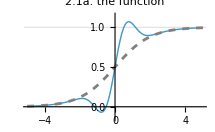
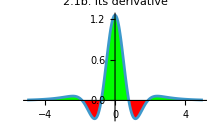
-Graphics- | -Graphics-Figure 2.1. A sigmoidal function that is not monotone

```mathematica
(*c.2.2*)
figure[{{
   Plot[{s2[t], LogisticSigmoid[t]}, {t, -5, 5},
    PlotStyle -> {Thick, Directive[Gray, Dashed]},
    GridLines -> {None, {0, 1}}, PlotRange -> {-0.15, 1.15},
    PlotLegends -> Placed[LineLegend[{"σ + sin(t) exp(-t.b2)",
        "logistic"}, LabelStyle -> Directive[figFont - 3]], Below],
    Evaluate@panel[PlotLabel -> "2.1a. the function"]],
   Plot[Evaluate@D[s2[t], t], {t, -5, 5}, PlotRange -> All,
    Filling -> Axis, FillingStyle -> {Red, Green},
    Evaluate@panel[PlotLabel -> "2.1b. its derivative"]]}},
 "Figure 2.1. A sigmoidal function that is not monotone"]
```

Cybenko's Theorem M2 needs only continuity and the two limits of Eq. (M1). Monotonicity is never used: Lemma M1 needs only that s(λt) tends to the step as λ → ∞, for every t ≠ 0, with s bounded. Figure 2.2 shows exactly that. The overshoot keeps its height, 0.068, but is pushed into a window of width about 1/λ around 0. By contrast Theorem M6, of Hornik, Stinchcombe and White, assumes a squashing function, which is nondecreasing, and so does not apply to s. Theorems M7 and M8 do apply, since s is bounded, continuous and not a polynomial.

Figure 2.2. s(λt) for λ = 1, 4, 16 against the step (dashed).

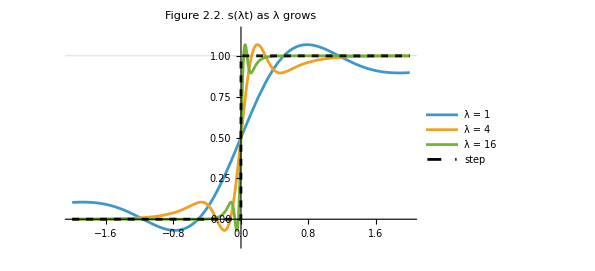

```mathematica
(*c.2.3*)
(* steepening: s2(λt) tends to the step except at t = 0; the
   overshoot keeps its height and moves into t = 0 *)
(* numeric copy of s that avoids underflow of exp(-t^2) for large t *)
sNum[t_?NumericQ] := LogisticSigmoid[t] + Sin[t] Exp[-Min[t^2, 700]];
Plot[{sNum[t], sNum[4 t], sNum[16 t], UnitStep[t]},
 {t, -2, 2}, PlotRange -> {-0.15, 1.15}, Exclusions -> None,
 PlotStyle -> {Automatic, Automatic, Automatic,
   Directive[Black, Dashed]}, GridLines -> {None, {0, 1}},
 PlotLegends -> Placed[LineLegend[{"λ = 1", "λ = 4", "λ = 16", "step"},
    LabelStyle -> figStyle, LegendLayout -> "Row"], Below],
 PlotLabel -> "Figure 2.2. s(λt) as λ grows", LabelStyle -> figStyle,
 ImageSize -> wFull]
```

### Does the staircase converge?

Build the staircase of Eq. (M7) from s instead of σ. Compared with the ideal staircase S_N of Eq. (1.3), each step now has a wiggle of relative size up to 0.068 on either side. Splitting the error as in Problem 1 gives the bound

|G_N(x)-f(x)|≤ω_f(1/(2N))+K_s ω_f(1/N)
K_s=sup_x ∑_k |s(λ(x-c_k))-H(x-c_k)|        (2.2)

The first term is the ideal staircase, Eq. (7.1) below. The second collects all the steps, each of height |Δ_k| ≤ ω_f(1/N). With λ = c N the constant K_s depends only on s and c, not on N, because |s(u) - H(u)| decays fast (here like e^-u). So the error is O(ω_f(1/N)), the same order as for the logistic. Only the constant changes.

Figure 2.3. Left: G_10 for example A built from the logistic and from s, with a deliberately soft λ = 40 so that the wiggles are visible. Right: a zoom.

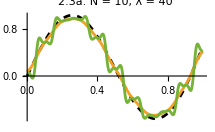
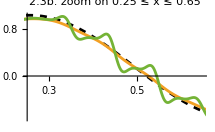
-Graphics- | -Graphics-Figure 2.3. Staircases from the non-monotone S-shape

```mathematica
(*c.2.4*)
(* the same function, safe for whole arrays of large arguments *)
s2v = Function[t, LogisticSigmoid[t] + Sin[t] Exp[-Clip[t^2, {0, 700}]]];
gS = stairOn[s2v, f[nodes[10]], 40, xsFine];
gL = stairOn[LogisticSigmoid, f[nodes[10]], 40, xsFine];
figure[{{
   ListLinePlot[{Transpose[{xsFine, f[xsFine]}],
     Transpose[{xsFine, gL}], Transpose[{xsFine, gS}]},
    PlotStyle -> {Directive[Black, Dashed], Automatic, Automatic},
    PlotLegends -> Placed[LineLegend[{"f", "logistic", "non-monotone"},
       LabelStyle -> Directive[figFont - 3]], Below],
    Evaluate@panel[PlotLabel -> "2.3a. N = 10, λ = 40"]],
   ListLinePlot[{Transpose[{xsFine, f[xsFine]}],
     Transpose[{xsFine, gL}], Transpose[{xsFine, gS}]},
    PlotRange -> {{0.25, 0.65}, All},
    PlotStyle -> {Directive[Black, Dashed], Automatic, Automatic},
    Ticks -> {{0.3, 0.4, 0.5, 0.6}, Automatic},
    Evaluate@panel[PlotLabel -> "2.3b. zoom on 0.25 ≤ x ≤ 0.65"]]}},
 "Figure 2.3. Staircases from the non-monotone S-shape"]
```

To test how much the wiggle matters, Table 2.2 uses the family σ(t) + A sin(t) exp(-t^2) with amplitude A = 0 (the logistic), A = 1 (the function of the problem) and A = 3, which overshoots to 1.85 and -0.85.

Table 2.2. Sup-norm error of G_N for example A, λ = 20 N, three amplitudes A.

```mathematica
(*c.2.5*)
(* the family σ + A sin(t) exp(-t.b2): A = 0 is the logistic *)
sA[a_] := Function[t,
   LogisticSigmoid[t] + a Sin[t] Exp[-Clip[t^2, {0, 700}]]];
nsA = {5, 10, 20, 40, 80, 160};
errA = Table[a -> Table[supErrS[sA[a], f, n, 20 n], {n, nsA}],
   {a, {0, 1, 3}}] // Association;
table[Join[{Prepend[("N = " <> ToString[#] &) /@ nsA, "A"]},
   Table[Prepend[NumberForm[#, 3] & /@ errA[a], a], {a, {0, 1, 3}}],
   {Prepend[NumberForm[#, 3] & /@ (errA[1]/errA[0]), "ratio A=1 / A=0"]}],
 "Table 2.2"]
```

A | N = 5 | N = 10 | N = 20 | N = 40 | N = 80 | N = 160
0 | 0.442 | 0.22 | 0.11 | 0.0551 | 0.0276 | 0.0138
1 | 0.714 | 0.377 | 0.191 | 0.096 | 0.0391 | 0.0195
3 | 1.6 | 0.915 | 0.466 | 0.233 | 0.0977 | 0.0489
ratio A=1 / A=0 | 1.62 | 1.71 | 1.73 | 1.74 | 1.42 | 1.42Table 2.2

Figure 2.4. The same errors on log-log axes. All three lines are parallel to slope -1 (dashed).

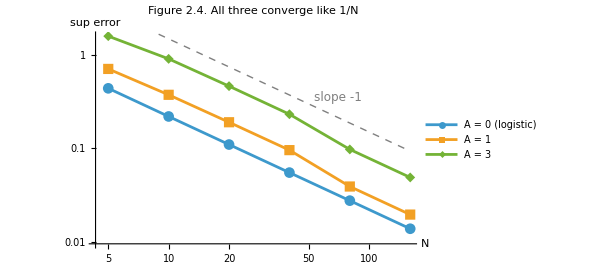

```mathematica
(*c.2.6*)
ListLogLogPlot[Table[Transpose[{nsA, errA[a]}], {a, {0, 1, 3}}],
 Joined -> True, PlotMarkers -> Automatic,
 AxesLabel -> {"N", "sup error"},
 Epilog -> {logLine[{{5, 3.}, {160, 3./32}}],
   logText["slope -1", {70, 0.35}]},
 PlotLegends -> Placed[LineLegend[{"A = 0 (logistic)", "A = 1", "A = 3"},
    LabelStyle -> figStyle, LegendLayout -> "Row"], Below],
 PlotLabel -> "Figure 2.4. All three converge like 1/N",
 LabelStyle -> figStyle, ImageSize -> wFull]
```

### Answer

Yes, σ(t) + sin(t) exp(-t^2) is sigmoidal: its limits are 0 and 1, and Eq. (M1) asks for nothing else. It is not monotone. It overshoots to 1.068 and -0.068. Yes, the staircase still converges, at the same rate O(1/N) as the logistic staircase, with an error about 1.4 to 1.7 times larger (Table 2.2). Even A = 3 converges. The reason is Eq. (2.2): every wiggle is scaled by a jump Δ_k of f, and the jumps shrink like ω_f(1/N). This is the content of Cybenko's theorem, which asks for continuity and the two limits, and not for monotonicity.

## 3. Problem 3: the polynomial activation t^2

Problem 3. Try the least-squares fit of section 5 (Table M4) with σ(t) = t^2, a polynomial. The error stops improving. Which of Theorems M1–M8 explains this?

### The experiment

Cells c.12–c.14 of the main notebook are repeated with the activation as a parameter: random inner weights y_j, θ_j in [-6, 6], least-squares outer weights α_j, 2000 training and 2000 test points, target g(x, y) = sin(πx) cos(πy) on [-1, 1].b2. Besides t^2 we also try t^3.

Table 3.1. Maximum and RMS test errors for N hidden units, three activations.

```mathematica
(*c.3.1*)
(* section 5 of the main notebook (c.12-c.14), with the activation as
   a parameter. PseudoInverse gives the least-squares α even when the
   columns of the hidden matrix are linearly dependent, as for t^2 *)
g[x_, y_] := Sin[Pi x] Cos[Pi y];
SeedRandom[3];
trainPts = RandomReal[{-1, 1}, {2000, 2}];
testPts = RandomReal[{-1, 1}, {2000, 2}];
hiddenA[act_][pts_, Yin_, th_] :=
  act[pts . Transpose[Yin] + ConstantArray[th, Length[pts]]];
fitA[act_, nh_] := Module[
   {Yr = RandomReal[{-6, 6}, {nh, 2}], th = RandomReal[{-6, 6}, nh], a},
   a = PseudoInverse[hiddenA[act][trainPts, Yr, th]] .
     (g @@@ trainPts);
   {Yr, th, a}];
testErr[act_, nh_] := With[{m = fitA[act, nh]}, Module[{r},
    r = hiddenA[act][testPts, m[[1]], m[[2]]] . m[[3]] - g @@@ testPts;
    {Max@Abs[r], Sqrt@Mean[r^2]}]];
acts = <|"logistic" -> LogisticSigmoid, "t.b2" -> (#^2 &),
   "t.b3" -> (#^3 &)|>;
nsQ = {2, 4, 6, 10, 20, 50, 100, 200};
SeedRandom[7];
errQ = Association@Table[k -> Table[testErr[acts[k], nh], {nh, nsQ}],
    {k, Keys[acts]}];
table[Prepend[
  Table[Join[{nh}, Flatten@Table[NumberForm[#, 3] & /@
       errQ[k][[Position[nsQ, nh][[1, 1]]]], {k, Keys[acts]}]],
   {nh, nsQ}],
  {"N", "logistic max", "logistic RMS", "t.b2 max", "t.b2 RMS",
   "t.b3 max", "t.b3 RMS"}], "Table 3.1"]
```

N | logistic max | logistic RMS | t.b2 max | t.b2 RMS | t.b3 max | t.b3 RMS
2 | 1.12 | 0.505 | 1.02 | 0.507 | 1.06 | 0.493
4 | 1.08 | 0.417 | 1.03 | 0.508 | 1.08 | 0.502
6 | 0.894 | 0.427 | 1.07 | 0.508 | 1.8 | 0.408
10 | 1.14 | 0.353 | 1.07 | 0.508 | 1.34 | 0.331
20 | 0.355 | 0.0898 | 1.07 | 0.508 | 1.34 | 0.331
50 | 0.118 | 0.0162 | 1.07 | 0.508 | 1.34 | 0.331
100 | 0.00832 | 0.0009 | 1.07 | 0.508 | 1.34 | 0.331
200 | 0.0003 | 0.0000175 | 1.07 | 0.508 | 1.34 | 0.331Table 3.1

The logistic error keeps falling, from 0.5 to 2 × 10^-5 in RMS. The t^2 error is stuck at 0.508 from the start, and the t^3 error drops once, to 0.331, at N = 10, and then stops for good. Adding units does nothing.

### Why: the network is a polynomial

With σ(t) = t^2 every hidden unit is the square of an affine function, and expanding the square gives only the monomials 1, x, y, x^2, x y, y^2:

∑_(j=1)^N α_j (y_j1 x+y_j2 y+θ_j)^2=a_0+a_1 x+a_2 y+a_3 x^2+a_4 xy+a_5 y^2        (3.1)

However many units there are, the network is a polynomial of degree at most 2, an element of a 6-dimensional space. With t^3 it is a polynomial of degree at most 3. In general the polynomials of degree at most k in n variables form a space of dimension

dim P_k(ℝ^n)=(n+k
k),    n=2:  k=2⇒6,  k=3⇒10        (3.2)

Adding units adds columns to the 2000 × N hidden matrix, but beyond 6 (or 10) columns they are linear combinations of the earlier ones. The rank stops growing, Table 3.3, and the singular values beyond the 6th (or 10th) are zero up to rounding, Figure 3.2. The least-squares fit can then do no better than the best polynomial of that degree. That polynomial can be computed exactly by projecting g onto the monomials in the mean square over [-1, 1].b2:

p_2=0,    p_3=(45x(1-3 y^2))/(2 π^3)        (3.3)

The best quadratic is zero. g is odd in x and even in y, so the only quadratic monomial that could match it is x, and its coefficient contains the integral of cos(πy) over [-1, 1], which is 0. The RMS error of the zero polynomial is the RMS of g itself, 1/2. The cubic picks up x and x y^2, and its error is 0.331. Both agree with the plateaus of Table 3.1; the small differences come from using 2000 sample points instead of the integral.

Table 3.2. Best polynomial approximations of degree 2 and 3, their RMS errors, and the plateaus of Table 3.1.

```mathematica
(*c.3.2*)
(* the best polynomial approximations of degree 2 and 3 in L.b2([-1,1].b2),
   computed exactly by projection *)
proj[basis_] := Module[{gram, rhs},
   gram = Outer[Integrate[#1 #2, {x, -1, 1}, {y, -1, 1}] &, basis, basis];
   rhs = Integrate[# g[x, y], {x, -1, 1}, {y, -1, 1}] & /@ basis;
   Simplify[LinearSolve[gram, rhs] . basis]];
poly[k_] := Flatten@Table[x^i y^j, {i, 0, k}, {j, 0, k - i}];
best2 = proj[poly[2]];
best3 = proj[poly[3]];
(* exact RMS error over the square *)
rmsOf[p_] := N@Sqrt[Integrate[Expand[(g[x, y] - p)^2],
      {x, -1, 1}, {y, -1, 1}]/4];
table[{{"degree", "monomials", "best polynomial", "RMS error",
   "plateau of Table 3.1"},
  {2, Length[poly[2]], TraditionalForm[best2], NumberForm[rmsOf[best2], 4],
   NumberForm[Last[errQ["t.b2"]][[2]], 4]},
  {3, Length[poly[3]], TraditionalForm[best3], NumberForm[rmsOf[best3], 4],
   NumberForm[Last[errQ["t.b3"]][[2]], 4]}}, "Table 3.2"]
```

degree | monomials | best polynomial | RMS error | plateau of Table 3.1
2 | 6 | 0 | 0.5 | 0.5083
3 | 10 | (45 x (1-3 y^2))/(2 π^3) | 0.331 | 0.3311Table 3.2

Figure 3.1. RMS test error against N. Dashed horizontal lines: the errors 0.5 and 0.331 of the best quadratic and cubic. Dashed vertical lines: N = 6 and N = 10, the dimensions of Eq. (3.2).

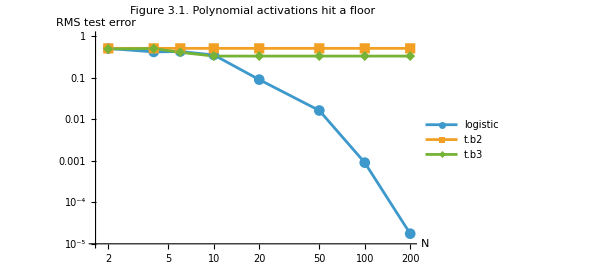

```mathematica
(*c.3.3*)
ListLogLogPlot[Table[Transpose[{nsQ, errQ[k][[All, 2]]}],
   {k, Keys[acts]}],
 Joined -> True, PlotMarkers -> Automatic, PlotRange -> {10^-5, 1},
 AxesLabel -> {"N", "RMS test error"},
 GridLines -> {{6, 10}, {rmsOf[best2], rmsOf[best3]}},
 GridLinesStyle -> Directive[Gray, Dashed],
 PlotLegends -> Placed[LineLegend[Keys[acts], LabelStyle -> figStyle,
    LegendLayout -> "Row"], Below],
 PlotLabel -> "Figure 3.1. Polynomial activations hit a floor",
 LabelStyle -> figStyle, ImageSize -> wFull]
```

Table 3.3. Rank of the hidden matrix. The logistic columns stay independent; the t^2 and t^3 columns saturate at 6 and 10.

```mathematica
(*c.3.4*)
(* rank of the 2000 x N hidden matrix: t^2 and t^3 saturate at 6 and 10 *)
SeedRandom[5];
rk[act_, nh_] := MatrixRank[hiddenA[act][trainPts,
    RandomReal[{-6, 6}, {nh, 2}], RandomReal[{-6, 6}, nh]],
   Tolerance -> 10^-9];
table[Prepend[
  Table[{nh, rk[LogisticSigmoid, nh], rk[acts["t.b2"], nh],
    rk[acts["t.b3"], nh]}, {nh, {4, 6, 8, 10, 20, 50}}],
  {"N", "rank, logistic", "rank, t.b2", "rank, t.b3"}], "Table 3.3"]
```

N | rank, logistic | rank, t.b2 | rank, t.b3
4 | 4 | 4 | 4
6 | 6 | 6 | 6
8 | 8 | 6 | 8
10 | 10 | 6 | 10
20 | 20 | 6 | 10
50 | 50 | 6 | 10Table 3.3

Figure 3.2. Singular values of the hidden matrix for N = 40, relative to the largest. For t^2 and t^3 they collapse to rounding level after the 6th and the 10th.

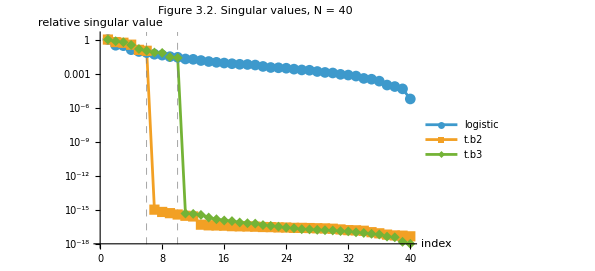

```mathematica
(*c.3.5*)
SeedRandom[5];
svals[act_] := Module[{yr = RandomReal[{-6, 6}, {40, 2}],
    th = RandomReal[{-6, 6}, 40], m},
   m = hiddenA[act][trainPts, yr, th];
   SingularValueList[m, Tolerance -> 0]/First@SingularValueList[m, 1]];
ListLogPlot[Table[Max[#, 10.^-18] & /@ svals[acts[k]], {k, Keys[acts]}],
 Joined -> True, PlotMarkers -> Automatic, PlotRange -> {10^-18, 2},
 AxesLabel -> {"index", "relative singular value"},
 GridLines -> {{6, 10}, None}, GridLinesStyle -> Directive[Gray, Dashed],
 PlotLegends -> Placed[LineLegend[Keys[acts], LabelStyle -> figStyle,
    LegendLayout -> "Row"], Below],
 PlotLabel -> "Figure 3.2. Singular values, N = 40",
 LabelStyle -> figStyle, ImageSize -> wFull]
```

Figure 3.3. The target g and what the three networks learn with N = 200. The logistic network reproduces g; the t^2 network gives a nearly flat surface (the sampled best quadratic, close to 0); the t^3 network gives the cubic of Eq. (3.3).

```mathematica
(*c.3.6*)
SeedRandom[8];
surf[fun_, lbl_] := Plot3D[fun[x, y], {x, -1, 1}, {y, -1, 1},
   PlotRange -> {-1.1, 1.1}, ColorFunction -> "TemperatureMap",
   PlotPoints -> 25, Ticks -> {{-1, 0, 1}, {-1, 0, 1}, {-1, 0, 1}},
   Evaluate@panel[PlotLabel -> lbl]];
netFun[act_, nh_] := With[{m = fitA[act, nh]},
   Function[{x, y}, First[hiddenA[act][{{x, y}}, m[[1]], m[[2]]] .
      m[[3]]]]];
{fSq, fCu, fLo} = {netFun[acts["t.b2"], 200], netFun[acts["t.b3"], 200],
   netFun[LogisticSigmoid, 200]};
figure[{
  {surf[g, "3.3a. target g"], surf[fLo, "3.3b. logistic, N = 200"]},
  {surf[fSq, "3.3c. t.b2, N = 200"], surf[fCu, "3.3d. t.b3, N = 200"]}},
 "Figure 3.3. What the networks learn"]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-Figure 3.3. What the networks learn

### Which theorem?

Theorem M8 (Leshno, Lin, Pinkus and Schocken) explains it. One-hidden-layer networks are universal if and only if the activation is not a polynomial. Its "only if" direction is exactly Eq. (3.1): with a polynomial activation of degree k the network can only make polynomials of degree at most k, a finite-dimensional space, which cannot approximate every continuous function.

Theorems M1–M4 of Cybenko do not apply, since t^2 is not sigmoidal: both its limits are +∞. But a theorem that does not apply says nothing about failure; Cybenko gives sufficient conditions only.

Theorems M6 and M7 also do not apply (t^2 is neither squashing nor bounded), and they too only give sufficient conditions. Only Theorem M8 is an "if and only if".

### Answer

With σ(t) = t^2 every network is a quadratic polynomial, Eq. (3.1), whatever N is. The least-squares error stops at that of the best quadratic, which for this g is the zero polynomial with RMS error 1/2. With t^3 it stops at the best cubic, RMS 0.331. Theorem M8 of Leshno, Lin, Pinkus and Schocken explains this: one hidden layer is universal exactly when the activation is not a polynomial.

## 4. Problem 4: x y z as a Kolmogorov superposition

Problem 4. Write x y z as a superposition in the form of Eq. (M8), using one-variable functions and addition, valid for positive x, y, z.

### The solution

The logarithm turns a product into a sum, and the exponential turns it back:

xyz=exp(ln x+ln y+ln z),    x,y,z>0        (4.1)

This has the shape of Eq. (M8) with n = 3: inner functions applied to each variable separately, their sum, then one outer function. Eq. (M8) has 2n + 1 = 7 branches, q = 0, ..., 6; we need only the first and set the outer function of the others to zero:

Φ_0=exp,  ψ_(p,0)=ln,  Φ_q=0  for  q=1,…,6        (4.2)

The inner functions are continuous and increasing, as in Kolmogorov's theorem, but they are not universal: they were chosen for this f. Kolmogorov's theorem promises universal inner functions that work for every f, at the price of being very rough. Here a smooth, special-purpose choice is enough. Positivity is needed because ln is defined only for positive arguments: at x = 0 the inner value would be -∞.

Two checks: the identities used, symbolically.

```mathematica
(*c.4.1*)
(* the two identities behind the solution *)
<|"exp(ln x + ln y + ln z) = x y z, for x, y, z > 0" ->
   FullSimplify[Exp[Log[x] + Log[y] + Log[z]] == x y z,
    x > 0 && y > 0 && z > 0],
  "four cubes, Eq. (4.3), for all real x, y, z" ->
   Expand[((x + y + z)^3 - (x + y - z)^3 - (x - y + z)^3 +
        (x - y - z)^3)/24] == x y z|>
```

<|exp(ln x + ln y + ln z) = x y z, for x, y, z > 0→True,four cubes, Eq. (4.3), for all real x, y, z→True|>

Eq. (M8) for n = 3 with the functions of Eq. (4.2), checked symbolically and on 10000 random points of (0, 1].b3.

```mathematica
(*c.4.2*)
(* Eq. (8) of the main notebook for n = 3: 2n + 1 = 7 branches,
   q = 0, ..., 6. Branch 0 carries the product, the others are zero *)
psi[p_, q_] := If[q == 0, Log, (0 &)];   (* inner functions ψ_{p,q} *)
Phi[q_] := If[q == 0, Exp, (0 &)];       (* outer functions Φ_q *)
kolmogorov[xs_List] := Sum[
   Phi[q][Sum[psi[p, q][xs[[p]]], {p, 1, 3}]], {q, 0, 6}];
SeedRandom[4];
pts = RandomReal[{0.001, 1}, {10000, 3}];
<|"symbolic" -> FullSimplify[kolmogorov[{x, y, z}] == x y z,
    x > 0 && y > 0 && z > 0],
  "largest relative error on 10000 random points" ->
   Max@Abs[(kolmogorov /@ pts)/(Times @@@ pts) - 1]|>
```

<|symbolic→True,largest relative error on 10000 random points→1.77636×10^-15|>

Figure 4.1. Eq. (M8) as a network for n = 3, in the style of Figure M8. All seven branches are drawn; only the branch q = 0 (black edges, red nodes) does any work, and the other six have outer function 0.

```mathematica
(*c.4.3*)
(* Eq. (8) drawn as a network for n = 3, in the style of Figure M8.
   Black and red: the branch q = 0 that does the work. Gray: the six
   branches whose outer function is zero *)
psiV[p_, q_] := Subscript["ψ", ToString[p] <> ToString[q]];
edges = Flatten@{
    Table[DirectedEdge[Subscript["x", p], psiV[p, q]], {p, 3}, {q, 0, 6}],
    Table[DirectedEdge[psiV[p, q], Subscript["Φ", q]], {p, 3}, {q, 0, 6}],
    Table[DirectedEdge[Subscript["Φ", q], "f"], {q, 0, 6}]};
active = Flatten@{
    Table[DirectedEdge[Subscript["x", p], psiV[p, 0]], {p, 3}],
    Table[DirectedEdge[psiV[p, 0], Subscript["Φ", 0]], {p, 3}],
    DirectedEdge[Subscript["Φ", 0], "f"]};
(* one row per inner function, grouped by branch q *)
yPsi[p_, q_] := If[q == 0, -2 p, -(4 q + p + 4)];
coords = Join[
   Flatten@Table[psiV[p, q] -> {2, yPsi[p, q]}, {p, 3}, {q, 0, 6}],
   Table[Subscript["Φ", q] -> {4, yPsi[2, q]}, {q, 0, 6}],
   Table[Subscript["x", p] -> {0, -(8 p + 1)}, {p, 3}], {"f" -> {6, -14}}];
Graph[edges, VertexCoordinates -> coords,
 EdgeStyle -> Join[(# -> Directive[Black, Thick] &) /@ active,
   (# -> Directive[GrayLevel[0.82]] &) /@ Complement[edges, active]],
 VertexStyle -> Join[(# -> Red &) /@ {psiV[1, 0], psiV[2, 0], psiV[3, 0],
     Subscript["Φ", 0]}, Flatten@Table[psiV[p, q] -> GrayLevel[0.8],
     {p, 3}, {q, 6}], Table[Subscript["Φ", q] -> GrayLevel[0.8], {q, 6}]],
 VertexSize -> 0.6,
 VertexLabels -> Join[
   Table[psiV[p, 0] -> Placed["ln", Above], {p, 3}],
   {Subscript["Φ", 0] -> Placed["exp", Above]},
   Table[Subscript["Φ", q] -> Placed[Style["0", Gray], Above], {q, 6}],
   (# -> Placed[#, Above] &) /@ {Subscript["x", 1], Subscript["x", 2],
     Subscript["x", 3], "f"}],
 VertexLabelStyle -> Directive[Black, figFont - 2],
 ImageSize -> {wFull, Automatic}, AspectRatio -> 1.1,
 PlotLabel -> Style["Figure 4.1. x y z as a Kolmogorov network",
   figFont]]
```

-Graphics-

Figure 4.2. The path of the input (0.5, 0.4, 0.8) through the network. Left: the inner function ln at the three inputs. Right: the outer function exp at their sum.

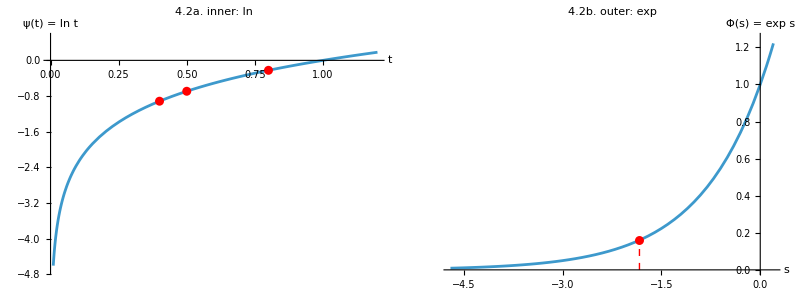
-Graphics-Figure 4.2. s = ln 0.5 + ln 0.4 + ln 0.8 = -1.833,  exp s = 0.16 = 0.5 × 0.4 × 0.8

```mathematica
(*c.4.4*)
(* the path of one input, (x, y, z) = (0.5, 0.4, 0.8), through the
   network: three inner values, one sum, one outer value *)
pt = {0.5, 0.4, 0.8}; sPt = Total@Log[pt];
figure[{{
   Plot[Log[t], {t, 0.01, 1.2}, PlotRange -> {-4.7, 0.5},
    AxesLabel -> {"t", "ψ(t) = ln t"},
    Epilog -> {Red, PointSize[0.03], Point[Transpose[{pt, Log[pt]}]]},
    Evaluate@panel[PlotLabel -> "4.2a. inner: ln"]],
   Plot[Exp[s], {s, -4.7, 0.2}, PlotRange -> {0, 1.25},
    AxesLabel -> {"s", "Φ(s) = exp s"},
    Epilog -> {Red, PointSize[0.03], Point[{sPt, Exp[sPt]}],
      Dashed, Line[{{sPt, 0}, {sPt, Exp[sPt]}}]},
    Evaluate@panel[PlotLabel -> "4.2b. outer: exp"]]}},
 Row[{"Figure 4.2. s = ln 0.5 + ln 0.4 + ln 0.8 = ",
   NumberForm[sPt, 4], ",  exp s = ", NumberForm[Exp[sPt], 4],
   " = 0.5 × 0.4 × 0.8"}]]
```

Geometrically the inner functions straighten the function. The level sets x y z = c are curved surfaces, but in the coordinates (ln x, ln y, ln z) they become the parallel planes u + v + w = ln c. After the inner functions, the function depends only on the sum of the coordinates, which is exactly what Eq. (M8) demands of each branch.

Figure 4.3. Left: the level sets x y z = 0.02, 0.1, 0.3. Right: the same sets after the inner functions, flat parallel planes.

```mathematica
(*c.4.5*)
(* level sets: x y z = c is curved; in the coordinates of the inner
   functions, (ln x, ln y, ln z), it is the flat plane u + v + w = ln c *)
levels = {0.02, 0.1, 0.3};
figure[{{
   ContourPlot3D[x y z, {x, 0.01, 1}, {y, 0.01, 1}, {z, 0.01, 1},
    Contours -> levels, Mesh -> None, ContourStyle -> Opacity[0.7],
    AxesLabel -> {"x", "y", "z"}, Ticks -> {{0, 1}, {0, 1}, {0, 1}},
    ViewPoint -> {2.6, 2.2, 1.6},
    Evaluate@panel[PlotLabel -> "4.3a. x y z = c"]],
   ContourPlot3D[u + v + w, {u, -4.6, 0}, {v, -4.6, 0}, {w, -4.6, 0},
    Contours -> Log[levels], Mesh -> None,
    ContourStyle -> Opacity[0.7], AxesLabel -> {"ln x", "ln y", "ln z"},
    Ticks -> {{-4, 0}, {-4, 0}, {-4, 0}}, ViewPoint -> {2.6, 2.2, 1.6},
    Evaluate@panel[PlotLabel -> "4.3b. in ln coordinates"]]}},
 "Figure 4.3. The inner functions straighten the level sets"]
```

-Graphics3D- | -Graphics3D-Figure 4.3. The inner functions straighten the level sets

### A version without positivity

Using cubes instead of the logarithm gives a superposition valid for all real x, y, z, zeros and negatives included:

xyz=1/24[(x+y+z)^3-(x+y-z)^3-(x-y+z)^3+(x-y-z)^3]        (4.3)

It uses four branches of Eq. (M8), with linear inner functions ±x, ±y, ±z and the outer functions ±s.b3/24. Since the inner functions are linear, this is also a network of the Cybenko form, Eq. (M3), with activation t^3 and four units. It is exact for this one product, while Problem 3 shows that the same activation cannot approximate functions in general. In the same way, the identity x y = ((x + y)^2 - (x - y)^2)/4 of c.16 in the main notebook is a two-branch superposition of the product of two variables.

The four-cube identity on 10000 random points of [-1, 1].b3, and at a point with a zero coordinate.

```mathematica
(*c.4.6*)
(* the four-cube form of Eq. (4.3) on [-1, 1].b3, zeros included:
   four branches with linear inner functions ±x and one outer
   function Φ(s) = ± s.b3/24 *)
cubeBranches[{x_, y_, z_}] := {(x + y + z)^3, -(x + y - z)^3,
    -(x - y + z)^3, (x - y - z)^3}/24;
SeedRandom[6];
pts3 = RandomReal[{-1, 1}, {10000, 3}];
<|"largest error on 10000 points of [-1, 1].b3" ->
   Max@Abs[(Total@*cubeBranches /@ pts3) - (Times @@@ pts3)],
  "at a point with a zero coordinate" ->
   Total@cubeBranches[{0., 0.7, -0.3}]|>
```

<|largest error on 10000 points of [-1, 1].b3→3.33067×10^-16,at a point with a zero coordinate→0.|>

### Answer

For positive x, y, z: x y z = exp(ln x + ln y + ln z), Eq. (4.1). In the form of Eq. (M8) with n = 3 this is the branch q = 0 with ψ_(p,0) = ln and Φ_0 = exp; the other six branches have Φ_q = 0, Eq. (4.2). For all real inputs, the four-cube identity Eq. (4.3) does the same with linear inner functions.

## 5. Problem 5: BasicRecurrentLayer as a Cybenko sum

Problem 5. Show that one step of BasicRecurrentLayer, tanh(W x + U h + b), is a Cybenko-type sum when you take (x, h) as the input. Draw its graph in the style of Figure M3. Which arrow would you add to make it recurrent?

### One step is a Cybenko sum

BasicRecurrentLayer with input size n and state size m computes, at each time t,

h_t=tanh(W x_t+U h_(t-1)+b)        (5.1)

with an m × n matrix W, an m × m matrix U and a bias vector b. Two facts turn this into Eq. (M3). First, tanh is a rescaled logistic, tanh s = 2σ(2s) - 1, Eq. (M2). Second, a constant is itself a hidden unit: -1 = -2σ(0·z + 0). Join the input and the old state into one vector z = (x_t, h_(t-1)) of length n + m. Then component i of the new state is

h_(t,i)=2σ(2(∑_k W_ik x_(t,k)+∑_l U_il h_(t-1,l)+b_i))-2σ(0)
=∑_j α_ij σ(y_j·z+θ_j),  z=(x_t,h_(t-1))∈ℝ^(n+m)        (5.2)

Each component is a sum of Eq. (M3) on the cube of inputs z. It uses two units: unit i, with inner weights y_i = 2(row i of W, row i of U), offset θ_i = 2b_i and outer weight 2, and a constant unit with y = 0, θ = 0 and outer weight -2. The whole new state is such a sum for each i, with the same hidden units shared and the outer weights α_ij = 2δ_ij. The step is a one-hidden-layer network in which the hidden layer and the output layer have the same size m. So by Theorem M2 a single step can be approximated in the other direction too: with enough units, a sum of this form can follow any continuous update rule for the state.

Both facts, checked symbolically.

```mathematica
(*c.5.1*)
(* the two facts used in Eq. (5.2): tanh is a rescaled logistic, and a
   constant is itself one hidden unit with zero input weights *)
<|"tanh s - (2 σ(2 s) - 1)" -> FullSimplify[
    TrigToExp[Tanh[s] - (2 LogisticSigmoid[2 s] - 1)]],
  "-1 = -2 σ(0 · z + 0)" -> (-1 == -2 LogisticSigmoid[0])|>
```

<|tanh s - (2 σ(2 s) - 1)→0,-1 = -2 σ(0 · z + 0)→True|>

A numerical check against the real layer. BasicRecurrentLayer is initialized with random weights, its biases are set to nonzero values, and it is run on a sequence of 40 inputs in three ways: by the layer itself, by the tanh recursion Eq. (5.1), and by the Cybenko sums Eq. (5.2).

Table 5.1. The weights of the layer and the agreement of the three computations. The layer computes in single precision, so it agrees with the other two to about 10^-7; the tanh recursion and the Cybenko sums agree to 10^-16.

```mathematica
(*c.5.2*)
(* a real BasicRecurrentLayer with input size n = 2 and state size m = 2;
   its weights, then three ways to run it on the same sequence *)
(* the initializer sets the biases to 0; give them nonzero values *)
rnn = NetReplacePart[
   NetInitialize[BasicRecurrentLayer[2, "Input" -> {"Varying", 2}],
    RandomSeeding -> 5], "Biases" -> {0.3, -0.4}];
{W, U, b} = Normal@NetExtract[rnn, #] & /@
   {"InputWeights", "StateWeights", "Biases"};
seq = Table[{Sin[t/3.], Cos[t/5.]}, {t, 40}];
(* 1: the layer itself *)
hLayer = rnn[seq];
(* 2: the recursion h_t = tanh(W x_t + U h_{t-1} + b), h_0 = 0 *)
hTanh = Rest@FoldList[Tanh[W . #2 + U . #1 + b] &, {0., 0.}, seq];
(* 3: the same step as a Cybenko sum of Eq. (5.2), input z = (x, h) *)
Yc = 2 Join[W, U, 2]; thc = 2 b;
cybenkoStep[h_, x_] := 2 LogisticSigmoid[Yc . Join[x, h] + thc] -
   2 LogisticSigmoid[0. Yc . Join[x, h]];
hCyb = Rest@FoldList[cybenkoStep, {0., 0.}, seq];
mat[m_] := MatrixForm[Map[NumberForm[#, 3] &, m, {-1}]];
table[{{"quantity", "value"},
  {"W (input weights)", mat[W]},
  {"U (state weights)", mat[U]},
  {"b (biases)", NumberForm[b, 3]},
  {"max |layer - tanh recursion|", sci@Max@Abs[hLayer - hTanh]},
  {"max |layer - Cybenko sums|", sci@Max@Abs[hLayer - hCyb]},
  {"max |tanh recursion - Cybenko sums|", sci@Max@Abs[hTanh - hCyb]}},
 "Table 5.1"]
```

quantity | value
W (input weights) | (2.45 | 1.06
0.101 | -0.02)
U (state weights) | (0.536 | -1.15
1.53 | -0.284)
b (biases) | {0.3,-0.4}
max |layer - tanh recursion| | 2.1×10^-7
max |layer - Cybenko sums| | 2.1×10^-7
max |tanh recursion - Cybenko sums| | 4.4×10^-16Table 5.1

### The graph

Figure 5.1. One step of BasicRecurrentLayer drawn like Figure M3, for n = m = 2. The four inputs on the left are the components of z = (x, h_old). The red labels are the weights: 2W_ik and 2U_il on the arrows into the hidden units, 2 on the arrows out. The offsets 2b_i and the constant unit giving -1 are not drawn, as θ_j is not drawn in Figure M3.

```mathematica
(*c.5.3*)
(* one step drawn like Figure M3: the input of the step is z = (x, h_old),
   four numbers; unit i computes σ(2 (W x + U h_old + b)_i), the output
   h_i = 2 (unit i) - 1. Offsets and the constant -1 are not drawn *)
ins = {"x1", "x2", "o1", "o2"};
insLbl = {Subscript["x", 1], Subscript["x", 2],
   Subsuperscript["h", 1, "old"], Subsuperscript["h", 2, "old"]};
wLbl[i_, k_] := Which[k <= 2, Row[{2, Subscript["W", 10 i + k]}],
   True, Row[{2, Subscript["U", 10 i + k - 2]}]];
e1 = Flatten@Table[DirectedEdge[ins[[k]], "u" <> ToString[i]],
    {k, 4}, {i, 2}];
e2 = Table[DirectedEdge["u" <> ToString[i], "h" <> ToString[i]], {i, 2}];
Graph[Join[e1, e2],
 VertexCoordinates -> Join[
   Table[ins[[k]] -> {0, 4.5 - 1.5 k}, {k, 4}],
   {"u1" -> {3.2, 1.5}, "u2" -> {3.2, -1.5}, "h1" -> {6, 1.5},
    "h2" -> {6, -1.5}}],
 VertexLabels -> Join[Thread[ins -> (Placed[#, Before] & /@ insLbl)],
   {"u1" -> Placed["σ", Above], "u2" -> Placed["σ", Below],
    "h1" -> Placed[Subscript["h", 1], After],
    "h2" -> Placed[Subscript["h", 2], After]}],
 VertexLabelStyle -> Directive[Black, figFont],
 EdgeLabels -> Join[
   Flatten@Table[DirectedEdge[ins[[k]], "u" <> ToString[i]] ->
      Placed[wLbl[i, k], 0.72], {k, 4}, {i, 2}],
   Table[DirectedEdge["u" <> ToString[i], "h" <> ToString[i]] ->
     Placed[2, 0.5], {i, 2}]],
 EdgeLabelStyle -> Directive[figFont - 3, Darker[Red],
   Background -> White],
 VertexSize -> 0.3, EdgeStyle -> Arrowheads[0.025],
 ImageSize -> wFull, PlotLabel ->
  Style["Figure 5.1. One step of BasicRecurrentLayer as Figure M3",
   figFont]]
```

-Graphics-

Read Figure 5.1 as Figure M3 was read in the main notebook. Information flows from left to right, each arrow multiplies by its weight, each hidden node adds what arrives and passes it through σ, and the arrows form a directed acyclic graph. Nothing in the picture is recurrent yet: h_old is just two more inputs.

### The arrow that makes it recurrent

The recurrence is the identification of h_old at time t with the output h at time t - 1. In the graph this means an arrow from each output node h_l back to the state units, carrying the weight U_il and crossed with a delay of one time step. These are the dashed blue arrows of Figure 5.2, including the self-loops U_11 and U_22. They make the graph cyclic, and this cycle is all that separates a recurrent layer from a feedforward one.

Figure 5.2. The recurrent layer folded into one picture. Black arrows: the input weights W_ik, as in Figure 5.1. Dashed blue arrows: the new arrows U_il from the state back into the state, each crossed one time step later.

```mathematica
(*c.5.4*)
(* the recurrent layer: the new arrows U_il run from the state units back
   into the state units, and each is crossed one time step later *)
recE = Join[
   Flatten@Table[DirectedEdge[Subscript["x", k], Subscript["h", i]],
     {k, 2}, {i, 2}],
   Flatten@Table[DirectedEdge[Subscript["h", l], Subscript["h", i]],
     {l, 2}, {i, 2}]];
Graph[recE,
 VertexCoordinates -> {Subscript["x", 1] -> {0, 1.5},
   Subscript["x", 2] -> {0, -1.5}, Subscript["h", 1] -> {3.5, 1.5},
   Subscript["h", 2] -> {3.5, -1.5}},
 VertexLabels -> {Subscript["x", 1] -> Placed[Subscript["x", 1], Before],
   Subscript["x", 2] -> Placed[Subscript["x", 2], Before],
   Subscript["h", 1] -> Placed[Subscript["h", 1], Above],
   Subscript["h", 2] -> Placed[Subscript["h", 2], Below]},
 VertexLabelStyle -> Directive[Black, figFont],
 EdgeStyle -> Join[
   Flatten@Table[DirectedEdge[Subscript["x", k], Subscript["h", i]] ->
      Directive[Black, Arrowheads[0.03]], {k, 2}, {i, 2}],
   Flatten@Table[DirectedEdge[Subscript["h", l], Subscript["h", i]] ->
      Directive[Blue, Dashed, Arrowheads[0.03]], {l, 2}, {i, 2}]],
 EdgeLabels -> Join[
   Flatten@Table[DirectedEdge[Subscript["x", k], Subscript["h", i]] ->
      Placed[Subscript["W", 10 i + k], 0.75], {k, 2}, {i, 2}],
   Flatten@Table[DirectedEdge[Subscript["h", l], Subscript["h", i]] ->
      Placed[Subscript["U", 10 i + l], 0.5], {l, 2}, {i, 2}]],
 EdgeLabelStyle -> Directive[figFont - 2, Darker[Red],
   Background -> White],
 VertexSize -> 0.12, ImageSize -> wFull,
 PlotLabel -> Style["Figure 5.2. The recurrent arrows (dashed blue)",
   figFont]]
```

-Graphics-

Unrolling removes the cycle again. Following the blue arrows forward in time gives a chain of copies of the same step, a deep feedforward network whose layers all share W, U and b:

h_t=F(x_t,h_(t-1))=F(x_t,F(x_(t-1),F(…)))        (5.3)

Figure 5.3. The recurrent layer unrolled over four time steps. Each blue arrow is a copy of the step of Figure 5.1; backpropagation through time follows these arrows backwards, as Eq. (M5) follows the arrows of Figure M3.

```mathematica
(*c.5.5*)
(* unrolled in time the loop disappears: a deep feedforward network in
   which every layer is the same Cybenko-type step, with shared W, U, b *)
T = 4;
unrolled = Join[
   Table[DirectedEdge[Subscript["x", t], Subscript["h", t]], {t, T}],
   Table[DirectedEdge[Subscript["h", t - 1], Subscript["h", t]], {t, T}]];
Graph[unrolled,
 VertexCoordinates -> Join[Table[Subscript["h", t] -> {2 t, 0}, {t, 0, T}],
   Table[Subscript["x", t] -> {2 t, -1.6}, {t, T}]],
 VertexLabels -> Placed["Name", Above],
 VertexLabelStyle -> Directive[Black, figFont],
 EdgeLabels -> Join[
   Table[DirectedEdge[Subscript["x", t], Subscript["h", t]] ->
     Placed["W", 0.5], {t, T}],
   Table[DirectedEdge[Subscript["h", t - 1], Subscript["h", t]] ->
     Placed["U", 0.5], {t, T}]],
 EdgeLabelStyle -> Directive[figFont - 2, Darker[Red],
   Background -> White],
 EdgeStyle -> Join[
   Table[DirectedEdge[Subscript["h", t - 1], Subscript["h", t]] ->
     Directive[Blue, Dashed, Arrowheads[0.03]], {t, T}],
   Table[DirectedEdge[Subscript["x", t], Subscript["h", t]] ->
     Directive[Black, Arrowheads[0.03]], {t, T}]],
 VertexSize -> 0.25, ImageSize -> wFull,
 PlotLabel -> Style["Figure 5.3. Unrolled over four time steps",
   figFont]]
```

-Graphics-

Figure 5.4. The two state components over 40 time steps: the layer (points) and the Cybenko sums of Eq. (5.2) (line).

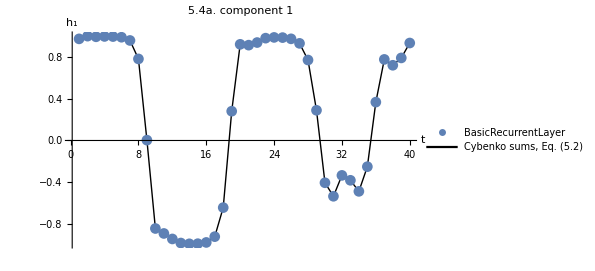
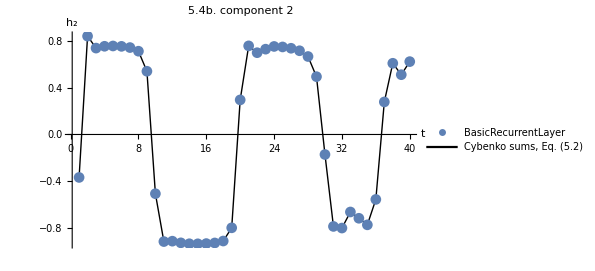
-Graphics-
-Graphics-Figure 5.4. The layer and the Cybenko sums give the same states

```mathematica
(*c.5.6*)
figure[Table[{
    ListPlot[{hLayer[[All, i]], hCyb[[All, i]]},
     Joined -> {False, True}, PlotMarkers -> {Automatic, None},
     PlotStyle -> {ColorData[97][1], Directive[Black, Thin]},
     AxesLabel -> {"t", Subscript["h", i]}, PlotRange -> All,
     PlotLegends -> Placed[LineLegend[{ColorData[97][1], Black},
        {"BasicRecurrentLayer", "Cybenko sums, Eq. (5.2)"},
        LabelStyle -> Directive[figFont - 3], LegendLayout -> "Row"],
       Below],
     PlotLabel -> "5.4" <> FromCharacterCode[96 + i] <>
       ". component " <> ToString[i],
     LabelStyle -> figStyle, ImageSize -> wFull]}, {i, 2}],
 "Figure 5.4. The layer and the Cybenko sums give the same states"]
```

### Answer

With z = (x, h) as the input, component i of tanh(W x + U h + b) equals 2σ(y_i·z + θ_i) - 2σ(0·z + 0) with y_i = 2(W_i, U_i) and θ_i = 2b_i, a sum of Eq. (M3), Eq. (5.2). Figure 5.1 draws it in the style of Figure M3, and Table 5.1 confirms it against BasicRecurrentLayer. To make it recurrent, add arrows from each state output h_l back into each state unit h_i, carrying U_il with a one-step delay (Figure 5.2).

## 6. Problem 6: the gradient with respect to the weights

Problem 6. Use Eq. (M5) to write ∂G/∂α_j and ∂G/∂y_ji, and check both against D as in c.7.

### The path rule for weights

Eq. (M5) gives the derivative of G with respect to an input as a sum, over all paths from that input to G, of the product of the local derivatives along the path. The same rule works for a weight. A weight sits on one arrow, so the paths start at that arrow. The derivative is the value at the tail of the arrow times the product of the local derivatives from its head to G. With z_j = y_j·x + θ_j and h_j = σ(z_j), as in Eq. (M4):

α_j sits on the arrow h_j → G. Its tail carries h_j = σ(z_j), and the head is G itself:

(∂G)/(∂α_j)=σ(z_j)        (6.1)

θ_j is the weight of an arrow from a constant input 1 to h_j. Its tail carries 1; from there the path passes through the node h_j (factor σ′(z_j)) and the arrow h_j → G (factor α_j):

(∂G)/(∂θ_j)=α_j σ'(z_j)        (6.2)

y_ji sits on the arrow x_i → h_j. Its tail carries x_i, and the path continues exactly as for θ_j:

(∂G)/(∂y_ji)=α_j σ'(z_j) x_i        (6.3)

Each weight lies on exactly one path to G, so each sum in Eq. (M5) has a single term. Eq. (6.3) is Eq. (6.2) times the input x_i. That is the familiar rule of backpropagation: the gradient of a weight is the signal flowing back to its head, α_j σ′(z_j), times the activity at its tail.

Table 6.1. The three formulas against D, for the random network of c.7 of the main notebook at the point x = (0.3, -0.7). Rows of the y matrix are the units j, columns the inputs i.

```mathematica
(*c.6.1*)
(* Eqs. (6.1)-(6.3) against automatic differentiation, for the same
   random network as c.7 of the main notebook (n = 2, N = 3) *)
Module[{Yw, th, al, x0, yv, tv, av, yy, tt, aa, gNet, rules, auto, z,
  sp, path, fmt},
 SeedRandom[2];
 Yw = RandomReal[{-2, 2}, {3, 2}];   (* weights y_ji *)
 th = RandomReal[{-1, 1}, 3];        (* offsets θ_j *)
 al = RandomReal[{-1, 1}, 3];        (* output weights α_j *)
 x0 = {0.3, -0.7};
 (* symbolic parameters, so that D can differentiate by them *)
 yv = Array[yy, {3, 2}]; tv = Array[tt, 3]; av = Array[aa, 3];
 gNet = av . LogisticSigmoid[yv . x0 + tv];
 rules = Join[Thread[Flatten[yv] -> Flatten[Yw]], Thread[tv -> th],
   Thread[av -> al]];
 auto = {D[gNet, {av}], D[gNet, {tv}], D[gNet, {yv}]} /. rules;
 (* the path products of Eqs. (6.1)-(6.3) *)
 z = Yw . x0 + th;
 sp = LogisticSigmoid[z] (1 - LogisticSigmoid[z]);   (* σ'(z_j) *)
 path = {LogisticSigmoid[z], al sp, Outer[Times, al sp, x0]};
 fmt[v_] := MatrixForm[Map[NumberForm[#, 4] &, v, {-1}]];
 table[Prepend[MapThread[{#1, fmt[#2], fmt[#3],
      sci@Max@Abs@Flatten[#2 - #3]} &,
    {{"∂G/∂αⱼ, Eq. (6.1)", "∂G/∂θⱼ, Eq. (6.2)",
      "∂G/∂yⱼᵢ, Eq. (6.3)"}, auto, path}],
   {"derivative", "D (automatic)", "path product", "difference"}],
  "Table 6.1"]]
```

derivative | D (automatic) | path product | difference
∂G/∂αⱼ, Eq. (6.1) | (0.6661
0.5169
0.7659) | (0.6661
0.5169
0.7659) | 0.
∂G/∂θⱼ, Eq. (6.2) | (0.1206
0.1391
-0.1708) | (0.1206
0.1391
-0.1708) | 0.
∂G/∂yⱼᵢ, Eq. (6.3) | (0.03618 | -0.08442
0.04174 | -0.09739
-0.05125 | 0.1196) | (0.03618 | -0.08442
0.04174 | -0.09739
-0.05125 | 0.1196) | 6.9×10^-18Table 6.1

### Using the gradient: training

These formulas are what gradient training needs. Fit G to f on points x_1, ..., x_M by least squares; the chain rule applied to the loss gives

L=1/M∑_(m=1)^M r_m^2,  r_m=G(x_m)-f(x_m)
(∂L)/(∂p)=2/M∑_(m=1)^M r_m (∂G)/(∂p)(x_m)        (6.4)

where ∂G/∂p is Eq. (6.1), (6.2) or (6.3). We train a network with one input, N = 8 hidden units and an output offset c on example A, f(x) = sin(2πx) + x.b2/2, at M = 200 points. The gradient of Eq. (6.4) is first checked against central finite differences of the loss.

The loss gradient from Eqs. (6.1)–(6.4) against finite differences, at random starting weights.

```mathematica
(*c.6.2*)
(* training data: example A of the main notebook on 200 points *)
xt = N@Range[0, 1, 1/199]; ft = f[xt]; nU = 8;
(* parameters in one vector p = (y_1..y_8, θ_1..θ_8, α_1..α_8, c) *)
unpack[p_] := {p[[1 ;; nU]], p[[nU + 1 ;; 2 nU]],
   p[[2 nU + 1 ;; 3 nU]], p[[-1]]};
netOut[p_, xs_] := Module[{y, t, a, c}, {y, t, a, c} = unpack[p];
   LogisticSigmoid[Outer[Times, xs, y] +
       ConstantArray[t, Length[xs]]] . a + c];
(* the loss of Eq. (6.4) and its gradient from Eqs. (6.1)-(6.3) *)
lossGrad[p_] := Module[{y, t, a, c, s, sa, r},
   {y, t, a, c} = unpack[p];
   s = LogisticSigmoid[Outer[Times, xt, y] + ConstantArray[t, Length[xt]]];
   sa = (s (1 - s)) . DiagonalMatrix[a];   (* α_j σ'(z_j) at each x *)
   r = s . a + c - ft;                      (* residuals *)
   {Mean[r^2], 2/Length[xt] Join[(r xt) . sa, r . sa, r . s, {Total[r]}]}];
(* check the whole gradient against central finite differences *)
SeedRandom[11];
p0 = Join[RandomReal[{-10, 10}, nU], RandomReal[{-5, 5}, nU],
   RandomReal[{-1, 1}, nU], {0.}];
fd = Table[(First@lossGrad[p0 + 10^-6 UnitVector[3 nU + 1, i]] -
      First@lossGrad[p0 - 10^-6 UnitVector[3 nU + 1, i]])/(2 10^-6),
   {i, 3 nU + 1}];
<|"largest |gradient - finite difference|" ->
   Max@Abs[fd - Last@lossGrad[p0]],
  "largest gradient entry" -> Max@Abs[Last@lossGrad[p0]]|>
```

<|largest |gradient - finite difference|→5.66865×10^-11,largest gradient entry→0.555811|>

Training uses gradient descent with the Adam update: each step moves the weights against a running average of the gradient, scaled by a running average of its size. The step size is 0.05/(1 + k/1000) at step k. The starting weights are random and far from good: y_j in [-10, 10], θ_j in [-5, 5], α_j in [-1, 1].

Table 6.2. The training history.

```mathematica
(*c.6.3*)
(* gradient descent with the Adam update (Kingma and Ba 2015) and a
   slowly decaying step; snapshots of p are kept for Figure 6.2 *)
train[p00_, steps_] := Module[{p = p00, m, v, l, gr, hist = {}, snaps},
   m = v = 0 p00; snaps = <|0 -> p00|>;
   Do[{l, gr} = lossGrad[p]; AppendTo[hist, l];
    m = 0.9 m + 0.1 gr; v = 0.999 v + 0.001 gr^2;
    p -= 0.05/(1 + k/1000.) (m/(1 - 0.9^k))/
       (Sqrt[v/(1 - 0.999^k)] + 10^-8);
    If[MemberQ[{30, 300, 6000}, k], snaps[k] = p], {k, steps}];
   {p, hist, snaps}];
{pT, lossHist, snaps} = train[p0, 6000];
table[Prepend[Table[{k, sci[lossHist[[k]]],
     sci@Sqrt[lossHist[[k]]]}, {k, {1, 10, 100, 1000, 3000, 6000}}],
  {"step", "loss (mean squared error)", "RMS error"}], "Table 6.2"]
```

step | loss (mean squared error) | RMS error
1 | 5.2×10^-1 | 7.2×10^-1
10 | 1.9×10^-1 | 4.4×10^-1
100 | 5.9×10^-2 | 2.4×10^-1
1000 | 3.4×10^-5 | 5.8×10^-3
3000 | 8.×10^-7 | 9.×10^-4
6000 | 1.8×10^-7 | 4.2×10^-4Table 6.2

Figure 6.1. The loss during training, on log-log axes. It falls by more than six orders of magnitude. The brief spikes near step 5000 are typical of Adam with a large step, and the loss recovers within a few steps.

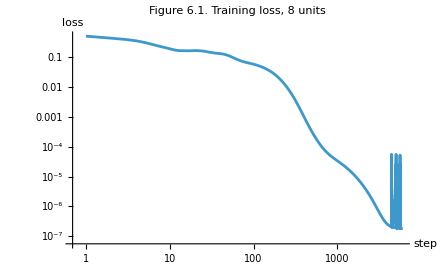

```mathematica
(*c.6.4*)
ListLogLogPlot[lossHist, Joined -> True, PlotRange -> All,
 AxesLabel -> {"step", "loss"},
 PlotLabel -> "Figure 6.1. Training loss, 8 units",
 LabelStyle -> figStyle, ImageSize -> wFull]
```

Figure 6.2. The network (solid) and f (dashed) at four moments of training.

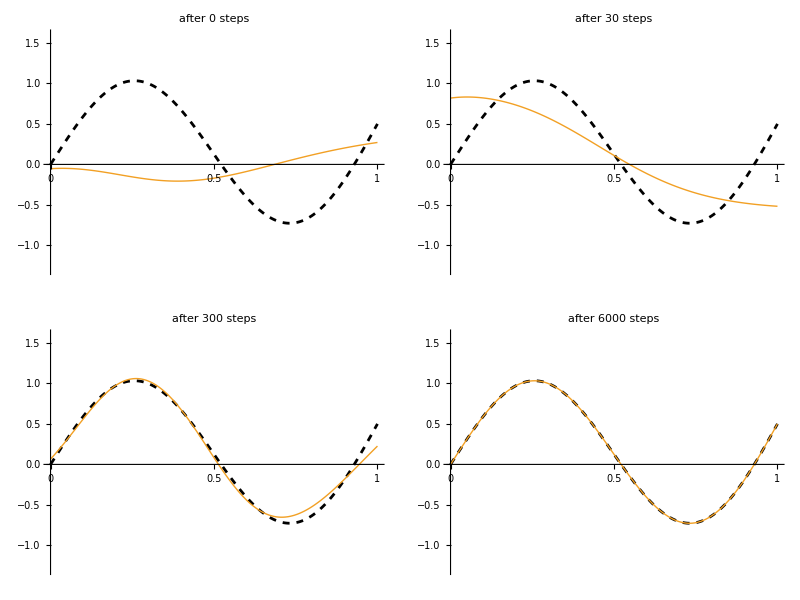
-Graphics-Figure 6.2. The network (solid) learning f (dashed)

```mathematica
(*c.6.5*)
snapPlot[k_] := ListLinePlot[{Transpose[{xt, ft}],
    Transpose[{xt, netOut[snaps[k], xt]}]},
   PlotStyle -> {Directive[Black, Dashed], Thick},
   PlotRange -> {-1.3, 1.6}, Ticks -> {{0, 0.5, 1}, Automatic},
   Evaluate@panel[PlotLabel -> "after " <> ToString[k] <> " steps"]];
figure[{{snapPlot[0], snapPlot[30]}, {snapPlot[300], snapPlot[6000]}},
 "Figure 6.2. The network (solid) learning f (dashed)"]
```

Figure 6.3. The trained network taken apart: the eight terms α_j σ(y_j x + θ_j) (thin) and their sum plus c, which is the fit (thick). The units do not look like the steps of a staircase. Training finds large terms that cancel and leave a precise curve.

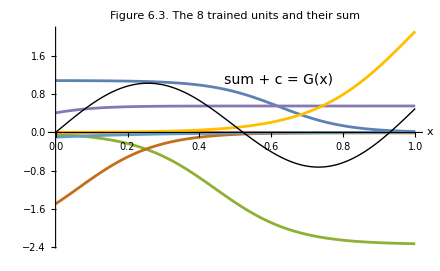

```mathematica
(*c.6.6*)
(* the trained network split into its 8 hidden units α_j σ(y_j x + θ_j);
   their sum plus the constant c is the fit *)
Module[{y, t, a, c, units},
 {y, t, a, c} = unpack[pT];
 units = Table[a[[j]] LogisticSigmoid[y[[j]] xt + t[[j]]], {j, nU}];
 ListLinePlot[Join[Transpose[{xt, #}] & /@ units,
   {Transpose[{xt, Total[units] + c}]}],
  PlotStyle -> Join[Table[ColorData[97][j], {j, nU}],
    {Directive[Black, Thick]}], PlotRange -> All,
  AxesLabel -> {"x", None},
  Epilog -> {Black, Text[Style["sum + c = G(x)", figFont], {0.62, 1.1}]},
  PlotLabel -> "Figure 6.3. The 8 trained units and their sum",
  LabelStyle -> figStyle, ImageSize -> wFull]]
```

Table 6.3. The trained 8-unit network against staircases of Eq. (M7) with 8 and 80 units.

```mathematica
(*c.6.7*)
(* trained weights against the staircase of Eq. (M7), on a fine grid *)
table[{{"construction", "units", "max error"},
  {"staircase, Eq. (M7)", 8, NumberForm[supErrS[LogisticSigmoid, f, 8,
     160], 3]},
  {"staircase, Eq. (M7)", 80, NumberForm[supErrS[LogisticSigmoid, f,
     80, 1600], 3]},
  {"trained with Eqs. (6.1)-(6.3)", 8, NumberForm[
    Max@Abs[netOut[pT, xsFine] - f[xsFine]], 3]}}, "Table 6.3"]
```

construction | units | max error
staircase, Eq. (M7) | 8 | 0.276
staircase, Eq. (M7) | 80 | 0.0276
trained with Eqs. (6.1)-(6.3) | 8 | 0.000808Table 6.3

The comparison makes the point of section 4 of the main notebook concrete. The staircase is a proof device: it shows that some weights exist. Trained weights are far better: 8 trained units reach an error of 8 × 10^-4, while the staircase needs 80 units for 0.028 and would need thousands to match.

### Answer

By the path rule of Eq. (M5): ∂G/∂α_j = σ(z_j), Eq. (6.1), and ∂G/∂y_ji = α_j σ′(z_j) x_i, Eq. (6.3), with z_j = y_j·x + θ_j; also ∂G/∂θ_j = α_j σ′(z_j), Eq. (6.2). They agree with D to 7 × 10^-18 (Table 6.1). Built into the loss gradient Eq. (6.4), they agree with finite differences to 10^-10 and train an 8-unit network to a maximum error of 8 × 10^-4.

## 7. Problem 7: rates from the modulus of continuity

Problem 7. Run the staircase of section 4 on x sin(1/x) (with value 0 at 0) and on the Cantor staircase of Figure M9. Predict the rate of convergence from the modulus of continuity, Eq. (M12), before you measure it.

Figure 7.1. The two targets, with zooms. x sin(1/x) oscillates infinitely often near 0 with amplitude x; the Cantor staircase C repeats itself at every scale.

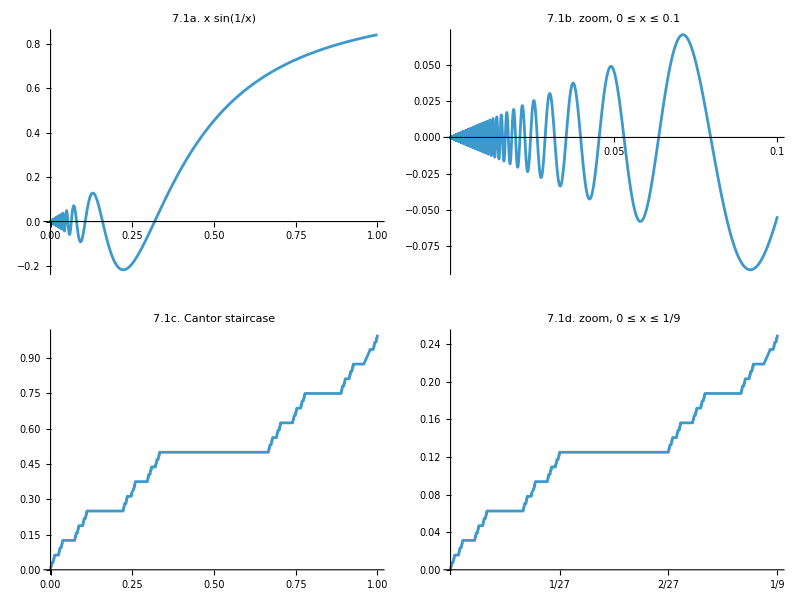
-Graphics-Figure 7.1. The two targets

```mathematica
(*c.7.1*)
(* the two functions, safe on whole arrays (x sin(1/x) is 0 at 0) *)
xsin[x_] := x Sin[1/(x + 10.^-300)];
cantor[x_] := CantorStaircase[x];
targets = <|"x sin(1/x)" -> xsin, "Cantor" -> cantor|>;
figure[{{
   Plot[xsin[x], {x, 0, 1}, PlotPoints -> 2000, PlotRange -> All,
    Evaluate@panel[PlotLabel -> "7.1a. x sin(1/x)"]],
   Plot[xsin[x], {x, 0, 0.1}, PlotPoints -> 2000, PlotRange -> All,
    Ticks -> {{0.05, 0.1}, Automatic},
    Evaluate@panel[PlotLabel -> "7.1b. zoom, 0 ≤ x ≤ 0.1"]]},
  {Plot[cantor[x], {x, 0, 1},
    Evaluate@panel[PlotLabel -> "7.1c. Cantor staircase"]],
   Plot[cantor[x], {x, 0, 1/9}, Ticks -> {{1/27, 2/27, 1/9}, Automatic},
    Evaluate@panel[PlotLabel -> "7.1d. zoom, 0 ≤ x ≤ 1/9"]]}},
 "Figure 7.1. The two targets"]
```

### The prediction

The ideal staircase S_N of Eq. (1.3) takes at x the value of f at the nearest node, which is at most 1/(2N) away. By the definition of the modulus of continuity, Eq. (M12),

|S_N(x)-f(x)|≤ω_f(1/(2N)),    error≈ω_f(1/(2N))        (7.1)

With λ = 20 N the logistic leakage is negligible (Problem 1), so the staircase error should be close to ω_f(1/(2N)). Its rate is the rate of ω_f. We work ω_f out for each target.

x sin(1/x). Near a point a > 0 the function oscillates with amplitude about a, and one half-oscillation, a change of 1/x by π, takes a change of x by about π a^2. A window of width δ placed where π a^2 = δ therefore sees the full swing from +a to -a, and no better placement exists: to the left the amplitude is smaller, to the right the window covers less than a half-oscillation. So

ω_f(δ)≈2 √(δ/π)    for  f(x)=x sin(1/x)        (7.2)

Rate prediction: ω_f(1/(2N)) ≈ 2√(1/(2πN)) = 0.80/√N, so the error should fall like N^(-1/2), one factor √2 for each doubling of N.

Cantor staircase. C satisfies the self-similarity C(x/3) = C(x)/2 and the symmetry C(1 - x) = 1 - C(x). An interval of length 3^-k rises by at most 2^-k, and the first interval [0, 3^-k] rises by exactly that:

C(x/3)=(C(x))/2,  C(1-x)=1-C(x)    ⇒    ω_C(3^-k)=2^-k        (7.3)

In between, ω_C(δ) stays within a factor 2 of δ to the power ln 2/ln 3 = 0.631, so C is Hölder continuous with that exponent and no better. Rate prediction:

ω_C(δ)≃δ^(ln 2/ln 3),    error∼N^(-1/2) and N^(-ln 2/ln 3)        (7.4)

The predictions are made. Now the measurements: first the moduli themselves, computed on a grid of 100001 points with a sliding maximum and minimum.

Table 7.1. The modulus of continuity ω_f(δ), measured and predicted by Eqs. (7.2) and (7.4).

```mathematica
(*c.7.2*)
(* modulus of continuity, Eq. (M12), on a grid of step h: the largest
   range max - min of f over a window of width δ *)
h = 10.^-5; grid = Range[0., 1., h];
fGrid = <|"x sin(1/x)" -> xsin[grid], "Cantor" -> cantor[grid]|>;
omegaG[vals_, d_] := With[{r = Round[d/(2 h)]},
   Max[MaxFilter[vals, r] - MinFilter[vals, r]]];
(* predictions, Eqs. (7.2) and (7.4) *)
omegaPred = <|"x sin(1/x)" -> (2 Sqrt[#/Pi] &),
   "Cantor" -> (#^(Log[2]/Log[3]) &)|>;
ds = 1./{5, 10, 20, 40, 80, 160, 320, 640};
table[Prepend[
  Flatten[Table[{
     {k, "measured", Sequence @@ (NumberForm[omegaG[fGrid[k], #], 3] &
         /@ ds)},
     {"", "predicted", Sequence @@ (NumberForm[omegaPred[k][#], 3] &
         /@ ds)}}, {k, Keys[targets]}], 1],
  Join[{"f", ""}, ("δ = 1/" <> ToString[Round[1/#]] &) /@ ds]],
 "Table 7.1"]
```

f |  | δ = 1/5 | δ = 1/10 | δ = 1/20 | δ = 1/40 | δ = 1/80 | δ = 1/160 | δ = 1/320 | δ = 1/640
x sin(1/x) | measured | 0.548 | 0.346 | 0.268 | 0.191 | 0.133 | 0.0951 | 0.0672 | 0.0475
 | predicted | 0.505 | 0.357 | 0.252 | 0.178 | 0.126 | 0.0892 | 0.0631 | 0.0446
Cantor | measured | 0.25 | 0.2 | 0.125 | 0.0667 | 0.0625 | 0.0313 | 0.0215 | 0.0156
 | predicted | 0.362 | 0.234 | 0.151 | 0.0975 | 0.063 | 0.0407 | 0.0263 | 0.017Table 7.1

Figure 7.2. The moduli on log-log axes, with lines of slope 1/2 and ln 2/ln 3 (dashed).

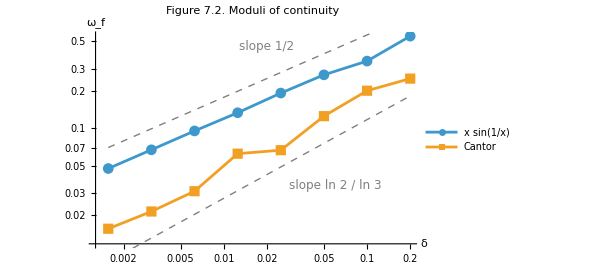

```mathematica
(*c.7.3*)
ListLogLogPlot[Table[Table[{d, omegaG[fGrid[k], d]}, {d, ds}],
   {k, Keys[targets]}],
 Joined -> True, PlotMarkers -> Automatic,
 AxesLabel -> {"δ", Subscript["ω", "f"]},
 Epilog -> {logLine[{{1/640, 0.07}, {1/5, 0.07 Sqrt[128]}}],
   logLine[{{1/640, 0.0085}, {1/5, 0.0085 128^(Log[2]/Log[3])}}],
   logText["slope 1/2", {0.02, 0.45}],
   logText["slope ln 2 / ln 3", {0.06, 0.035}]},
 PlotLegends -> Placed[LineLegend[Keys[targets], LabelStyle -> figStyle,
    LegendLayout -> "Row"], Below],
 PlotLabel -> "Figure 7.2. Moduli of continuity",
 LabelStyle -> figStyle, ImageSize -> wFull]
```

### The measurement

The staircase of Eq. (M7) with λ = 20 N, measured on a grid that has a spacing of 2 × 10^-5 on [0, 0.3], where x sin(1/x) oscillates fastest. For the Cantor staircase we use both N = 3^k, which fits its self-similarity, and the values of N used for x sin(1/x).

Table 7.2. The prediction ω_f(1/(2N)) of Eq. (7.1) against the measured error. The ratio is never above 1: Eq. (7.1) is an upper bound that is nearly attained.

```mathematica
(*c.7.4*)
(* the prediction, made before measuring:
   error ≈ ω_f(1/(2N)), Eq. (7.1) *)
nsP = {5, 10, 20, 40, 80, 160, 320, 640};
nsC = 3^Range[6];
predErr[k_, n_] := omegaG[fGrid[k], 1./(2 n)];
(* the measurement: sup error of the staircase of Eq. (M7), λ = 20 N,
   on a grid that is dense where x sin(1/x) oscillates *)
xsM = Union[Range[0., 0.3, 2.*^-5], Range[0.3, 1., 2.*^-4]];
fM = #[xsM] & /@ targets;   (* f on that grid, computed once *)
measErr[k_, n_] := Max@Abs[fM[k] - stairOn[LogisticSigmoid,
      targets[k][nodes[n]], 20 n, xsM]];
errTab = <|
   "x sin(1/x)" -> Table[{n, predErr["x sin(1/x)", n],
      measErr["x sin(1/x)", n]}, {n, nsP}],
   "Cantor" -> Table[{n, predErr["Cantor", n], measErr["Cantor", n]},
     {n, Join[nsC, nsP]}]|>;
table[Prepend[
  Flatten[KeyValueMap[Function[{k, rows},
     Table[{If[i == 1, k, ""], rows[[i, 1]], NumberForm[rows[[i, 2]], 3],
       NumberForm[rows[[i, 3]], 3], NumberForm[rows[[i, 3]]/rows[[i, 2]],
        3]}, {i, Length[rows]}]], errTab], 1],
  {"f", "N", "predicted ω(1/(2N))", "measured error", "ratio"}],
 "Table 7.2"]
```

f | N | predicted ω(1/(2N)) | measured error | ratio
x sin(1/x) | 5 | 0.346 | 0.311 | 0.901
 | 10 | 0.268 | 0.185 | 0.691
 | 20 | 0.191 | 0.148 | 0.772
 | 40 | 0.133 | 0.104 | 0.78
 | 80 | 0.0951 | 0.081 | 0.852
 | 160 | 0.0672 | 0.0528 | 0.786
 | 320 | 0.0475 | 0.0431 | 0.908
 | 640 | 0.0336 | 0.0316 | 0.94
Cantor | 3 | 0.25 | 0.233 | 0.931
 | 9 | 0.125 | 0.116 | 0.931
 | 27 | 0.0625 | 0.0582 | 0.931
 | 81 | 0.0313 | 0.0291 | 0.931
 | 243 | 0.0156 | 0.0145 | 0.93
 | 729 | 0.00781 | 0.00727 | 0.931
 | 5 | 0.2 | 0.136 | 0.682
 | 10 | 0.125 | 0.111 | 0.889
 | 20 | 0.0667 | 0.0617 | 0.926
 | 40 | 0.0625 | 0.0408 | 0.653
 | 80 | 0.0313 | 0.0292 | 0.936
 | 160 | 0.0215 | 0.0155 | 0.722
 | 320 | 0.0156 | 0.0118 | 0.752
 | 640 | 0.00781 | 0.00765 | 0.979Table 7.2

Table 7.3. Rates: the exponent predicted from ω, the slope of the predicted errors, and the slope of the measured errors, by least squares in log-log coordinates.

```mathematica
(*c.7.5*)
(* rates: least-squares slopes of log(error) against log N *)
slope[pts_] := Coefficient[Fit[Log[pts], {1, t}, t], t];
rateRows = {
   {"x sin(1/x)", "N = 5 ... 640", -1/2,
    slope[errTab["x sin(1/x)"][[All, {1, 2}]]],
    slope[errTab["x sin(1/x)"][[All, {1, 3}]]]},
   {"Cantor", "N = 3 ... 729", -Log[2]/Log[3],
    slope[errTab["Cantor"][[1 ;; 6, {1, 2}]]],
    slope[errTab["Cantor"][[1 ;; 6, {1, 3}]]]},
   {"Cantor", "N = 5 ... 640", -Log[2]/Log[3],
    slope[errTab["Cantor"][[7 ;;, {1, 2}]]],
    slope[errTab["Cantor"][[7 ;;, {1, 3}]]]}};
table[Prepend[{#1, #2, Row[{TraditionalForm[#3], " = ", NumberForm[N[#3],
        3]}], NumberForm[#4, 3], NumberForm[#5, 3]} & @@@ rateRows,
  {"f", "range", "rate from ω", "slope of ω(1/(2N))",
   "slope of measured error"}], "Table 7.3"]
```

f | range | rate from ω | slope of ω(1/(2N)) | slope of measured error
x sin(1/x) | N = 5 ... 640 | -1/2 = -0.5 | -0.489 | -0.458
Cantor | N = 3 ... 729 | -(log(2))/(log(3)) = -0.631 | -0.631 | -0.631
Cantor | N = 5 ... 640 | -(log(2))/(log(3)) = -0.631 | -0.639 | -0.616Table 7.3

Figure 7.3. Measured errors (marks) and the predictions ω_f(1/(2N)) (dashed).

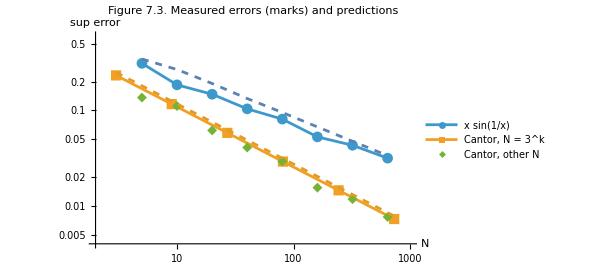

```mathematica
(*c.7.6*)
Show[
 ListLogLogPlot[{errTab["x sin(1/x)"][[All, {1, 3}]],
   errTab["Cantor"][[1 ;; 6, {1, 3}]],
   errTab["Cantor"][[7 ;;, {1, 3}]]},
  Joined -> {True, True, False}, PlotMarkers -> Automatic,
  PlotRange -> {{2, 1000}, {0.004, 0.6}},
  AxesLabel -> {"N", "sup error"},
  PlotLegends -> Placed[LineLegend[{"x sin(1/x)", "Cantor, N = 3^k",
      "Cantor, other N"}, LabelStyle -> Directive[figFont - 3],
     LegendLayout -> "Row"], Below],
  PlotLabel -> "Figure 7.3. Measured errors (marks) and predictions",
  LabelStyle -> figStyle, ImageSize -> wFull],
 ListLogLogPlot[{errTab["x sin(1/x)"][[All, {1, 2}]],
   errTab["Cantor"][[1 ;; 6, {1, 2}]]}, Joined -> True,
  PlotStyle -> {Directive[ColorData[97][1], Dashed],
    Directive[ColorData[97][2], Dashed]}]]
```

Figure 7.4. Where the error lives. For x sin(1/x) it is largest around x ≈ 0.1, where the oscillations are as wide as the steps; for the Cantor staircase it sits on the rising parts, the Cantor set, and is zero on the flat parts.

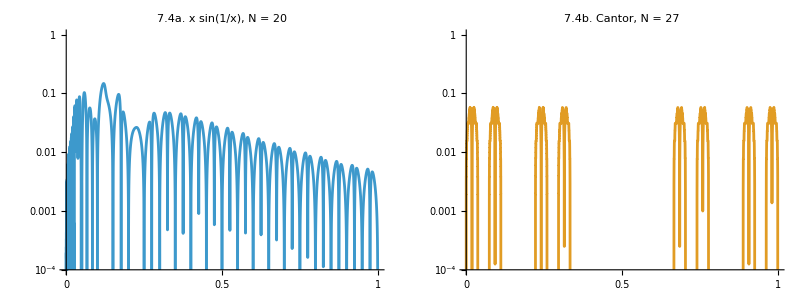
-Graphics-Figure 7.4. The staircase error |f - G| along x

```mathematica
(*c.7.7*)
(* where the error lives: |f - G_N| along x, N = 20 and N = 27 *)
figure[{{
   ListLogPlot[Transpose[{xsM, Abs[xsin[xsM] - stairOn[LogisticSigmoid,
         xsin[nodes[20]], 400, xsM]] + 10.^-12}], Joined -> True,
    PlotRange -> {10^-4, 1}, Ticks -> {{0, 0.5, 1}, Automatic},
    Evaluate@panel[PlotLabel -> "7.4a. x sin(1/x), N = 20"]],
   ListLogPlot[Transpose[{xsM, Abs[cantor[xsM] - stairOn[LogisticSigmoid,
         cantor[nodes[27]], 540, xsM]] + 10.^-12}], Joined -> True,
    PlotRange -> {10^-4, 1}, Ticks -> {{0, 0.5, 1}, Automatic},
    PlotStyle -> ColorData[97][2],
    Evaluate@panel[PlotLabel -> "7.4b. Cantor, N = 27"]]}},
 "Figure 7.4. The staircase error |f - G| along x"]
```

### Answer

x sin(1/x): predicted ω(δ) ≈ 2√(δ/π), so the error should behave like N^(-1/2). Measured slope -0.46 over N = 5 ... 640, a little flatter than -1/2 because the error approaches the bound ω_f(1/(2N)) from below: their ratio drifts upward, from 0.69–0.78 at N = 10–40 to 0.94 at N = 640.

Cantor staircase: predicted ω(3^-k) = 2^-k, so the error should behave like N to the power -ln 2/ln 3 = -0.631. Measured slope -0.631 for N = 3^k, where the error is exactly 0.931 ω_C(1/(2N)) at every k, and -0.62 for the other N.

Both functions are continuous on [0, 1], so by Theorem M9 they are uniformly continuous, ω_f(1/N) → 0, and the staircase converges, as Cybenko's theorem requires. The modulus of continuity predicts the rate: neither function is Lipschitz, and both converge more slowly than the O(1/N) of the smooth example A.

## References

S Shape Functions Theory, the main notebook: D. O Shayda, N. Hoshino, Computational Classnotes (2026).

G. Cybenko, Approximation by superpositions of a sigmoidal function, Math. Control Signals Systems 2 (1989) 303–314. doi:10.1007/BF02551274

K. Hornik, M. Stinchcombe, H. White, Multilayer feedforward networks are universal approximators, Neural Networks 2 (1989) 359–366. doi:10.1016/0893-6080(89)90020-8

K. Hornik, Approximation capabilities of multilayer feedforward networks, Neural Networks 4 (1991) 251–257.

M. Leshno, V. Ya. Lin, A. Pinkus, S. Schocken, Multilayer feedforward networks with a nonpolynomial activation function can approximate any function, Neural Networks 6 (1993) 861–867. doi:10.1016/S0893-6080(05)80131-5

A. N. Kolmogorov, On the representation of continuous functions of many variables by superposition of continuous functions of one variable and addition, Dokl. Akad. Nauk SSSR 114 (1957) 953–956.

D. E. Rumelhart, G. E. Hinton, R. J. Williams, Learning representations by back-propagating errors, Nature 323 (1986) 533–536. doi:10.1038/323533a0

D. P. Kingma, J. Ba, Adam: A method for stochastic optimization, ICLR 2015, arXiv:1412.6980.

P. J. Werbos, Backpropagation through time: what it does and how to do it, Proc. IEEE 78 (1990) 1550–1560. doi:10.1109/5.58337

Wolfram Research, BasicRecurrentLayer, Wolfram Language documentation, reference.wolfram.com/language/ref/BasicRecurrentLayer.html

© Computational Classnotes · CC BY-NC-SA 4.0